# Convergence of Data Driven Coefficients

## for 2 D Tipping Cascade Data

## Function Initializations

## Making Windows

Starting from first data point.
Does not give the total number of windows possible.

```mathematica
MakeWindow[Data_,WL_,Overlap_,l_]:=
Module[{Lb,Hb,WO,TP},
TP=Length[Data];
WO=Floor[(1-Overlap)*WL];
Lb=1+((l-1)*WO);
Hb=(WL+((l-1)*WO));
(*{Lb,Hb}*)
Data[[Lb;;Hb]]
]
```

## Data Driven Reconstruction

### Core Function for Tipping Cascades

Here we are assuming all second order coefficients are zero and in third order coefficients all but the self interaction coefficient () are zero.
This gives an dataset (association) for each i (node name).
First element is R (not r but all zeroth order parts combined), and last element is  () term (a).
We have n+2 elements.

-Graphics-

```mathematica
TippingCoefsBasic[TimeSerieValues_,i_,dt_]:=(Module[{Y,Mat,Dim,TP,MatrixRowDef,MatrixRow,Coefs,CoefKeys},
Dim=Dimensions[Values[TimeSerieValues]];
TP=Dim[[2]];



CoefKeys=Join[{"\*SubscriptBox[R, "<>StringDelete[ToString[i]," "]<>"]"},Table["\*SubscriptBox[x, "<>StringDelete[ToString[j]," "]<>"]",{j,Keys[TimeSerieValues]}],{"\*SubscriptBox[x, "<>StringDelete[ToString[i]," "]<>"]"<>"^3"}];

MatrixRowDef=Join[{Table[1,TP]},Values[TimeSerieValues]];

MatrixRow=Join[MatrixRowDef,{TimeSerieValues[i]^3}];

Mat=Join[Table[MatrixRow.MatrixRowDef[[k]]/TP,{k,1,Dim[[1]]+1}],{MatrixRow.TimeSerieValues[i]^2/TP}];

Y=Join[Table[(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).MatrixRowDef[[k]][[;;-2]]/(TP-1),{k,1,Dim[[1]]+1}],{(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).TimeSerieValues[i][[;;-2]]^2/(TP-1)}];

Coefs=Association[Table[CoefKeys[[h]]->(LinearSolve[Mat,Y]/dt)[[h]],{h,1,Dim[[1]]+2}]];

Dataset[Coefs]
]
)
```

### Tipping Cascade Coefficients + Windowing

```mathematica
TippingCoefsWithWindow[TimeSerieValues_,i_,l_,dt_,WL_,Overlap_]:=(Module[{WindowTimeSerieValues,WindowTimeSerieValuesShuffle,Coefs,Errors,CoefsAfterError},

WindowTimeSerieValues=(MakeWindow[#,WL,Overlap,l]&)/@TimeSerieValues;

Coefs=TippingCoefsBasic[WindowTimeSerieValues,i,dt];

Coefs
]
)
```

## Generation of Data

This gives a temporal data for the tipping network.
It may be better to eliminate graph part and driver nodes and u.
We have the same problem of global variables x1, x2, ...
GenData format is in a way that data is n one dimensional timeseries.
We can have function for rm (but it does not show it as a time function in ItoProcess output ).
Data can be plotted with ListPlot, ListLinePlot and DateListPlot.
For now a, b, and x0 are set to be same for all nodes.

```mathematica
StochTippingDataGen[A_,SpecificGraph_,d_,TippedNodes_,rm_,DriverNodes_,UValue_,Noise_,dt_,InitVal_,FinalTime_]:=(Module[{n,B,r,eq,GenData,a=-1,b=1,x0=0},

n=Length[A];
r= Table[0&,n];

t=.;

r[[TippedNodes]]=rm;
B=A;
Do[B[[i,Complement[VertexOutComponent[SpecificGraph,i,1],{i}]]]=UValue,{i,DriverNodes}];



eq=Table[ⅆSymbol["x"<>ToString[i]][t]==(r[[i]][t]+b*(Symbol["x"<>ToString[i]][t]-x0)+a*(Symbol["x"<>ToString[i]][t]-x0)^3+d*Sum[Sqrt[-b/a]*Transpose[A][[i,j]],{j,1,n,1}]+d*Sum[Transpose[B][[i,j]]*(Symbol["x"<>ToString[j]][t]-x0),{j,1,n,1}])ⅆt+Noise*ⅆSymbol["w"<>ToString[i]][t],{i,1,n,1}];



GenData=RandomFunction[ItoProcess[eq,Table[Symbol["x"<>ToString[k]][t],{k,1,n}],{Table[Symbol["x"<>ToString[k]],{k,1,n}],InitVal},t,Table[Symbol["w"<>ToString[k]]\[Distributed]WienerProcess[],{k,1,n}]],{0.,FinalTime,dt},Method->"KloedenPlatenSchurz"];

GenData=TemporalData[Table[GenData["Values"][[;;,l]],{l,1,n}],{0,FinalTime}];

GenData
]
)
```

#### To not let error bars get negative

```mathematica
Clear[PosBar];
PosBar[y_]:=(Module[{x=y},
If[x[[2,1]]-x[[2,2]]<0,x[[2]]=Around[x[[2,1]],{x[[2,1]],x[[2,2]]}],x];
x
]
)
```

## Data

## Generate or Import

### Generate

#### Tipping Network

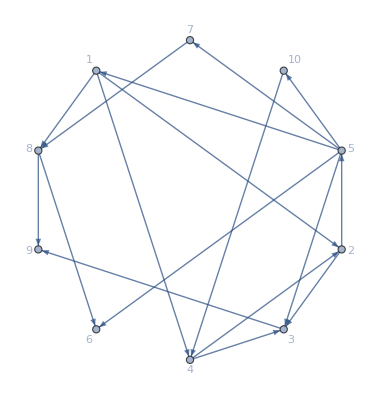

```mathematica
graph=Graph[{0->1,1->2,3->2,4->2,4->5,4->6,6->7,7->8,4->9,0->3,0->7,1->4,2->8,3->1,4->0,7->5,9->3}/.{0->1,1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->9,9->10},VertexLabels->Automatic,GraphLayout->"CircularEmbedding"]
```

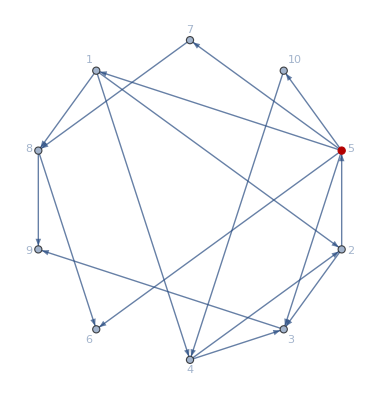

```mathematica
HighlightGraph[graph,5]
```

```mathematica
A=AdjacencyMatrix[graph]
```

SparseArray[…]

```mathematica
Export[NotebookDirectory[]<>"10D_Adjacency",A,"Table","FieldSeparators"->Tab]
```

C:\Users\alish\Desktop\stability paper\10D_Adjacency

```mathematica
Export[NotebookDirectory[]<>"10D_Network.pdf",HighlightGraph[graph,5]]
```

C:\Users\alish\Desktop\stability paper\10D_Network.pdf

#### SDE

```mathematica
MaTeX["\\begin{aligned}\\dot x_{i} &= r_i + b_{i}x_{i} + a_{i}x_{i}^3 + \\sum_{j=1}^{N} {d_{ij}x_{j}}\\end{aligned}",FontSize->15]
```

-Graphics-

For i=5  , and for other nodes 
If i!=j 
 if j is connected to i with a directed edge from j to i.

#### Data properties:

Diffusion is 
Initial values are 
All parameters are constant

```mathematica
A=AdjacencyMatrix[graph]//Normal;
```

```mathematica
SeedRandom[859];
Noise=√0.5;
dt=0.005;
GenData=StochTippingDataGen[A,graph,0.3,{5},0.79&,{1},1,Noise,dt,Table[1.2,10],50000]
```

TemporalData[<<10>>]

```mathematica
TimeSerieValues=Association[Table[ToString[i]->GenData["ValueList"][[i]],{i,1,10}]];
```

#### Read data here.

```mathematica
(*Export[NotebookDirectory[]<>"10node_0_005_50000_sqrt0_5.csv",Transpose@(Values@TimeSerieValues)]*)
```

C:\Users\alish\Desktop\stability paper\10node_0_005_50000_sqrt0_5.csv

```mathematica
TimeSerieValuesImported=Transpose@Import[NotebookDirectory[]<>"10node_0_005_50000_sqrt0_5.csv"];TimeSerieValues=Association[Table[ToString[i]->TimeSerieValuesImported[[i]],{i,1,10}]];
```

Part::partw: Part 3 of {{1.27, 1.24768, 1.22358, 1.21695, 1.18186, 1.17864, 1.15511, 1.10825, 0.980468, <<8>>, <<9999986>>, 1.71564, 1.7248, 1.69562, 1.7385, 1.67958}, <<1>>} does not exist.

Part::partw: Part 4 of {{1.27, 1.24768, 1.22358, 1.21695, 1.18186, 1.17864, 1.15511, 1.10825, 0.980468, <<8>>, <<9999986>>, 1.71564, 1.7248, 1.69562, 1.7385, 1.67958}, <<1>>} does not exist.

Part::partw: Part 5 of {{1.27, 1.24768, 1.22358, 1.21695, 1.18186, 1.17864, 1.15511, 1.10825, 0.980468, <<8>>, <<9999986>>, 1.71564, 1.7248, 1.69562, 1.7385, 1.67958}, <<1>>} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

## Visualization

```mathematica
g4=ListPlot[GenData["Paths"],
PlotRange->All,
ImageSize->Large,
AspectRatio->1/8.5,
PlotLabel->Style["A",FontFamily->"Times",12],
Axes->False,
Frame->True,
FrameTicks->{{{-1,1},None},{Table[i,{i,0,1000,100}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",12],
FrameLabel->{{{Style["t",12],Style["x1",12]},{None,Style["x2",12]}},{{Style["t",12],Style["x1",12]},{None,Style["x2",12]}}},
PlotStyle->{Thickness[0.002],Black},
PlotLayout->"Column",
Joined->True]
```

-Graphics-

## Windowing and Coefficients

### Window sizes

Here we choose window sizes (N) and find out how many of each N we can have and what is Min(N).
Our ensemble size (MN) is equal or less than Min(N).

```mathematica
TimePoints=10000000;
Overlap=70/100;
WLs=Floor[PowerRange[500,500000,1.2]/10]*10
(*Logarithmic x axis is better because we can reach to large N and still show the convergence and Delta is still clear(y can not be logarthmic)*)
```

{490,600,710,860,1030,1240,1490,1790,2140,2570,3090,3710,4450,5340,6410,7700,9240,11090,13310,15970,19160,23000,27600,33120,39740,47690,57230,68680,82420,98900,118680,142420,170910,205090,246110,295330,354400,425280}

```mathematica
(*WLs=Join[Table[i,{i,500,40500,1000}]]*)
```

{500,1500,2500,3500,4500,5500,6500,7500,8500,9500,10500,11500,12500,13500,14500,15500,16500,17500,18500,19500,20500,21500,22500,23500,24500,25500,26500,27500,28500,29500,30500,31500,32500,33500,34500,35500,36500,37500,38500,39500,40500}

```mathematica
(*WLs=Join[Table[i,{i,75000,500000,50000}],{400000}]*)
```

This finds total number of windows with size N which we can have in the specified “TimePoints”.

```mathematica
WindowNumbers=Table[With[{TP=TimePoints,Overlap=Overlap,WL=i},Floor[(TP-(Overlap*WL))/((1-Overlap)*WL)]],{i,WLs}]
```

{68024,55553,46946,38757,32360,26879,22369,18619,15573,12967,10785,8982,7488,6239,5197,4326,3605,3003,2502,2084,1737,1446,1205,1004,836,696,580,483,402,334,278,231,192,160,133,110,91,76}

```mathematica
WLsAndWindowNumbers=MapThread[List,{WLs,WindowNumbers}]
```

{{490,68024},{600,55553},{710,46946},{860,38757},{1030,32360},{1240,26879},{1490,22369},{1790,18619},{2140,15573},{2570,12967},{3090,10785},{3710,8982},{4450,7488},{5340,6239},{6410,5197},{7700,4326},{9240,3605},{11090,3003},{13310,2502},{15970,2084},{19160,1737},{23000,1446},{27600,1205},{33120,1004},{39740,836},{47690,696},{57230,580},{68680,483},{82420,402},{98900,334},{118680,278},{142420,231},{170910,192},{205090,160},{246110,133},{295330,110},{354400,91},{425280,76}}

```mathematica
(*MN=Last[WindowNumbers]*)
```

76

```mathematica
MN=50;(*ensemble size*)
```

### Coefficients for each N

```mathematica
SeedRandom[36];
WLsAndWindowSample=MapThread[List,{WLs,Table[RandomSample[Range[1,WL],MN],{WL,WindowNumbers}]}];
```

```mathematica
XmCoeffsAllWinSize=Table[Table[Table[Values@Normal[TippingCoefsWithWindow[TimeSerieValues,ToString[m],l,dt,WL[[1]],Overlap]],{l,WL[[2]]}],{WL,WLsAndWindowSample}],{m,1,10}];
```

Part::take: Cannot take positions 2697598 through 2698087 in {{1.27, 1.24768, 1.22358, 1.21695, 1.18186, 1.17864, 1.15511, 1.10825, 0.980468, <<9999987>>, 1.71564, 1.7248, 1.69562, 1.7385, 1.67958}, <<1>>}[[3]].

Part::take: Cannot take positions 2697598 through 2698087 in {{1.27, 1.24768, 1.22358, 1.21695, 1.18186, 1.17864, 1.15511, 1.10825, 0.980468, <<9999987>>, 1.71564, 1.7248, 1.69562, 1.7385, 1.67958}, <<1>>}[[4]].

Part::take: Cannot take positions 2697598 through 2698087 in {{1.27, 1.24768, 1.22358, 1.21695, 1.18186, 1.17864, 1.15511, 1.10825, 0.980468, <<9999987>>, 1.71564, 1.7248, 1.69562, 1.7385, 1.67958}, <<1>>}[[5]].

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 2 of {10} does not exist.

Table::nliter: Non-list iterator TP$1550608 at position 2 does not evaluate to a real numeric value.

Dot::rect: Nonrectangular tensor encountered.

Table::nliter: Non-list iterator TP$1550608 at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Part::partw: Part 2 of {10} does not exist.

## Convergence Plots for a, b, r and d

## Δa

```mathematica
leg=PointLegend[ColorData[97,"ColorList"],Range[1,10],LabelStyle->{10,FontFamily->"Times"},LegendLayout->{"Column",2}]
```

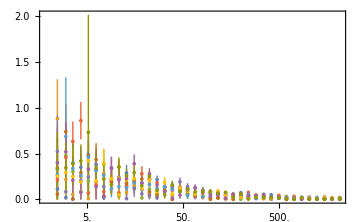

```mathematica
(*gadata=Table[MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[i]][[All,All,10+2]]))+1)}],{i,1,10}];*)
ga=ListPlot[Map[PosBar,gadata,{2}],Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["|\\Delta a|",FontSize->12]},(*PlotLabel->Style["A",15,FontFamily->"Times"],*)
PlotRange->All,
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
(*PlotLegends->Placed[Range[1,10],{0.5,0.9}],*)
(*,PlotStyle->{Black,Darker[Green]}*)
ImagePadding->{{55, 10}, {Automatic, Automatic}},
ImageSize->Medium
(*,PlotLegends->{Style[,12],Style[,12]}*)]
```

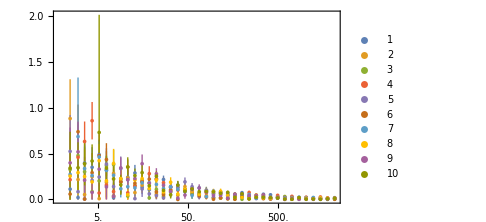

```mathematica
ga=Legended[ga,Placed[leg,{0.85,0.65}]]
```

```mathematica
Export[NotebookDirectory[]<>"10D_delta_a.pdf",ga]
```

C:\Users\alish\Desktop\stability paper\10D_delta_a.pdf

## Δb

```mathematica
MapThread[List,{WLs,Abs@((MeanAround/@(X1CoeffsAllWinSize[[All,All,2]]))-1)}]
```

{{500,5.72.5},{1500,1.01.1},{2500,1.10.8},{3500,0.70.9},{4500,1.60.8},{5500,0.500.27},{6500,1.120.34},{7500,0.850.27},{8500,0.910.29},{9500,0.90.4},{10500,0.50.4},{11500,0.600.30},{12500,0.380.19},{13500,0.650.31},{14500,0.500.35},{15500,0.370.22},{16500,0.200.17},{17500,0.490.25},{18500,0.890.29},{19500,0.300.14},{20500,0.650.15},{21500,0.360.29},{22500,0.440.23},{23500,0.460.25},{24500,0.080.12},{25500,0.190.13},{26500,0.610.22},{27500,0.420.14},{28500,0.030.13},{29500,0.570.20},{30500,0.370.28},{31500,0.550.12},{32500,0.220.16},{33500,0.230.12},{34500,0.260.16},{35500,0.090.15},{36500,0.490.14},{37500,0.140.10},{38500,0.060.11},{39500,0.100.12},{40500,0.090.18},{200000,0.070.04}}

```mathematica
(*gbdata=Table[MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[i]][[All,All,i+1]]))-1)}],{i,1,10}];*)
```

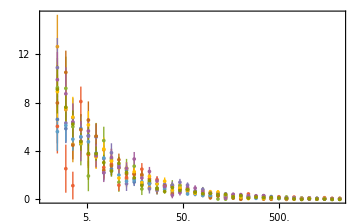

```mathematica
gb=ListPlot[Map[PosBar,gbdata,{2}],Frame->True,
(*FrameTicks->{{Automatic,None},{Automatic,None}},*)
FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["|\\Delta b|",FontSize->12]},(*PlotLabel->Style["B",15,FontFamily->"Times"],*)
PlotRange->All,
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
(*PlotLegends->Range[1,10],*)
ImageSize->Medium,
(*PlotStyle->{Black,Darker[Green]},*)
ImagePadding->{{55, 10}, {Automatic, Automatic}}]
```

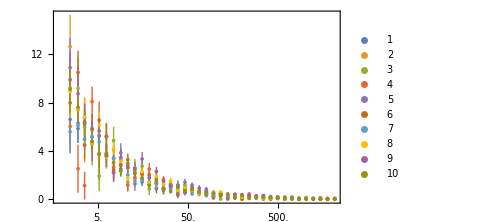

```mathematica
gb=Legended[gb,Placed[leg,{0.85,0.65}]]
```

```mathematica
Export[NotebookDirectory[]<>"10D_delta_b.pdf",gb]
```

C:\Users\alish\Desktop\stability paper\10D_delta_b.pdf

## Δd

```mathematica
AllEdges=Flatten[Table[{i,j},{i,1,10},{j,Select[Range[1,10],#!=i&]}],1]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,1},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,1},{3,2},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,1},{4,2},{4,3},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,1},{5,2},{5,3},{5,4},{5,6},{5,7},{5,8},{5,9},{5,10},{6,1},{6,2},{6,3},{6,4},{6,5},{6,7},{6,8},{6,9},{6,10},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,9},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,10},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9}}

```mathematica
OnEdges=Select[AllEdges,A[[#[[1]],#[[2]]]]!=0&];
```

```mathematica
OffEdges=Select[AllEdges,A[[#[[1]],#[[2]]]]==0&];
```

```mathematica
gcdata=Table[MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[s[[2]]]][[All,All,1+s[[1]]]]))-0.3A[[s[[1]],s[[2]]]])}],{s,OnEdges}]
```

```mathematica
legd=PointLegend[ColorData[97,"ColorList"],Table[MaTeX["d_{"<>ToString[s[[2]]]<>","<>ToString[s[[1]]]<>"}",FontSize->10],{s,OnEdges}],LabelStyle->{10,FontFamily->"Times"},LegendLayout->{"Column",3}]
```

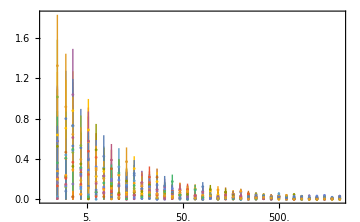

```mathematica
gc=ListPlot[Map[PosBar,gcdata,{2}],Frame->True,
(*FrameTicks->{{Automatic,None},{Automatic,None}},*)FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)(*{{500,0.5},{1000,1},{5000,5},{10^4,10},{5*10^4,50},{10^5,100}}*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["|\\Delta d|",FontSize->12]},
(*PlotLabel->Style["C",15,FontFamily->"Times"],*)
PlotRange->All,
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
ImageSize->Medium,
(*PlotLegends->Table[MaTeX["d_{"<>ToString[s[[2]]]<>","<>ToString[s[[1]]]<>"}"],{s,OnEdges}],*)
(*PlotStyle->{Black,Darker[Green]},*)
ImagePadding->{{55, 10}, {Automatic, Automatic}}]
```

```mathematica
gc=Legended[gc,Placed[legd,{0.75,0.65}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"10D_delta_d_nonzero.pdf",gc]
```

C:\Users\alish\Desktop\stability paper\10D_delta_d_nonzero.pdf

## Δr

```mathematica
MapThread[List,{WLs,Abs@((MeanAround/@(X1CoeffsAllWinSize[[All,All,1]]))-0.79)}]
```

{{500,5.52.1},{1500,0.91.1},{2500,1.50.8},{3500,1.00.7},{4500,1.40.7},{5500,0.580.29},{6500,0.590.30},{7500,0.560.20},{8500,0.840.28},{9500,0.680.32},{10500,0.460.23},{11500,0.450.27},{12500,0.240.16},{13500,0.500.22},{14500,0.540.31},{15500,0.300.23},{16500,0.110.10},{17500,0.430.23},{18500,0.600.22},{19500,0.150.13},{20500,0.470.17},{21500,0.250.25},{22500,0.300.14},{23500,0.340.23},{24500,0.160.11},{25500,0.110.10},{26500,0.430.17},{27500,0.190.10},{28500,0.020.10},{29500,0.350.19},{30500,0.340.22},{31500,0.400.11},{32500,0.320.13},{33500,0.100.07},{34500,0.220.12},{35500,0.090.14},{36500,0.260.13},{37500,0.170.07},{38500,0.060.08},{39500,0.100.07},{40500,0.070.14},{200000,0.0310.028}}

```mathematica
gddata=Table[MapThread[List,{WLs,Abs@((MeanAround/@(XmCoeffsAllWinSize[[i]][[All,All,1]]))-If[i==5,0.79+0.3*Sum[A[[j,i]],{j,1,10}],0.3*Sum[A[[j,i]],{j,1,10}]])}],{i,1,10}]
```

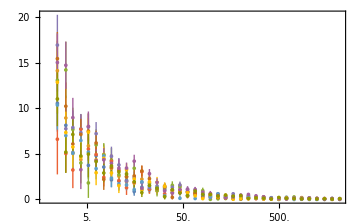

```mathematica
gd=ListPlot[Map[PosBar,gddata,{2}],Frame->True,(*FrameTicks->{{Automatic,None},{Automatic,None}},*)
FrameTicks->{{Automatic,None},{(*Table[{i,i/1000},{i,WLs[[;;;;8]]+500}]*)Table[{i,i dt},{i,PowerRange[1000,100000]}],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10],
FrameLabel->{MaTeX["T",FontSize->12],MaTeX["|\\Delta r|",FontSize->12]},(*PlotLabel->Style["D",15,FontFamily->"Times"],*)
PlotRange->All,
Joined->False,
IntervalMarkers->"Bars",
ScalingFunctions->{"Log",Automatic},
(*PlotLegends->Range[1,10],*)
ImageSize->Medium,
(*PlotStyle->{Black,Darker[Green]},*)
ImagePadding->{{55, 10}, {Automatic, Automatic}}]
```

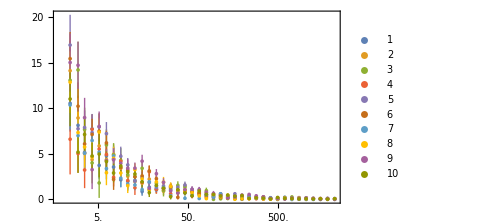

```mathematica
gd=Legended[gd,Placed[leg,{0.85,0.65}]]
```

```mathematica
Export[NotebookDirectory[]<>"10D_delta_r.pdf",gd]
```

C:\Users\alish\Desktop\stability paper\10D_delta_r.pdf

```mathematica
legend=PointLegend[ColorData[97,"ColorList"],Range[1,10],(*LegendMarkers->Graphics[{EdgeForm[None],Opacity[1],Disk[]}],*)LegendMarkerSize->10,LegendLayout->"Row",LegendFunction->(Framed[#,RoundingRadius->3,FrameStyle->LightGray]&),LegendMargins->1,LabelStyle->{12,FontFamily->"Times"}(*,LegendLabel->Placed[Style["no. fixed points",12],Below]*)]
```

```mathematica
gg=Legended[GraphicsColumn[{GraphicsRow[{ga,gb}],GraphicsRow[{gc,gd}]}],Placed[legend,Below]]
```

-Graphics-

## Results & Figures

For i=5  , and for other nodes 
If i!=j 
 if j is connected to i with a directed edge from j to i.

Diffusion is 
Initial values are 
All parameters are constant

### Figure Draft

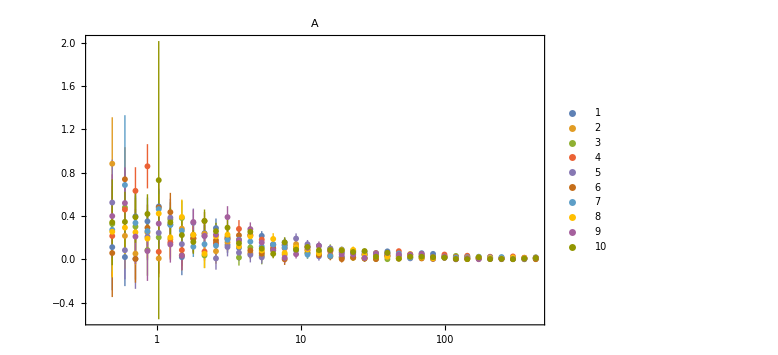

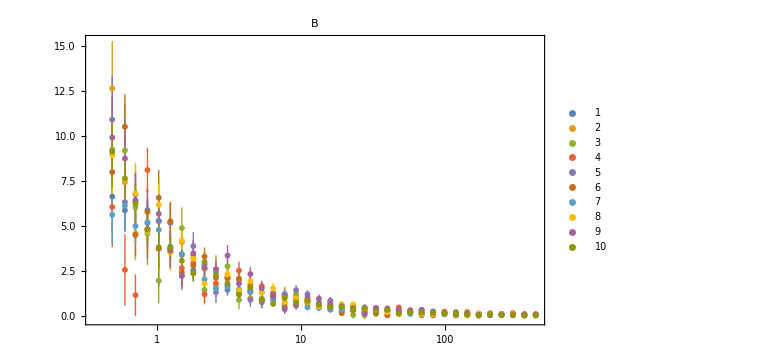

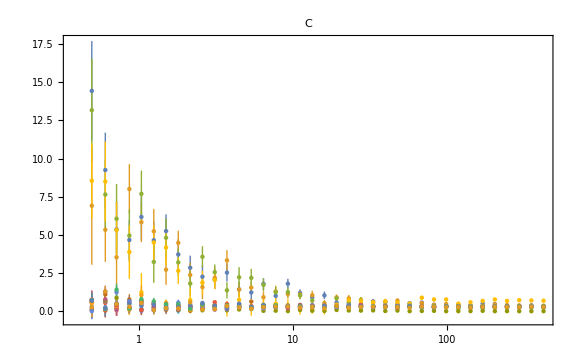

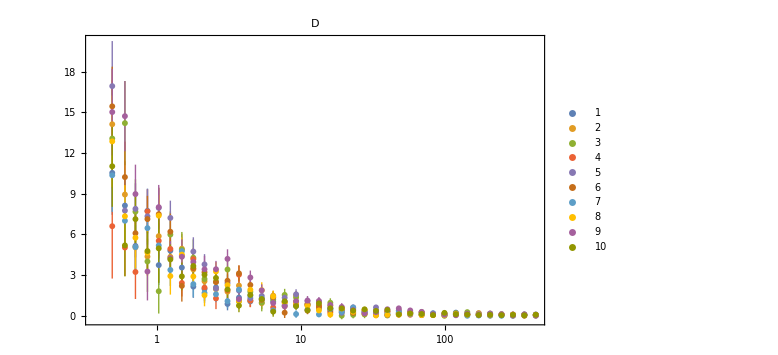

## Conclusion & Summary

We construct a long (10^7 data point) data for a unidirectional tipping system, and then we show that by increasing window size (N) all coefficients driven from data converge to the theoretical values by which data is constructed with. For every N we construct an ensemble of windows with 70% overlap. Ensembles are of the same size, 50. Each point on the figures is the average of the coefficient on the ensemble of size N. We see high accuracy for N>10^5.

### Latex Package

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
Needs["MaTeX`"]
```

```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\texlive\\2017\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.02.1\\bin\\gswin64c.exe"
]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\texlive\2017\bin\win32\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.02.1\bin\gswin64c.exe}

## Figure Data

```mathematica
gddata={{{490,Around[10.546397632686004,3.097854568883681]},{600,Around[8.134139624859952,2.104213091700019]},{710,Around[5.152020698513138,1.7811097666612692]},{860,Around[7.741535367046041,1.6422871827756718]},{1030,Around[3.7382500987882787,1.466262026002899]},{1240,Around[4.805908610968581,1.272417076751423]},{1490,Around[3.5574867416848113,0.9005255713562094]},{1790,Around[2.153771320355069,0.8253879611736573]},{2140,Around[1.9836655404728771,0.9011738990877832]},{2570,Around[2.0924206827654754,0.6275703942879461]},{3090,Around[0.8740832267990362,0.4697160133991402]},{3710,Around[1.3438715369758276,0.4743921420807153]},{4450,Around[1.0652631397288896,0.37815084117740266]},{5340,Around[1.1858345837176114,0.3430789314069225]},{6410,Around[1.0561169783286224,0.31278617042993323]},{7700,Around[1.0516774566779263,0.2127519569246171]},{9240,Around[0.7170972124273438,0.24112341903954282]},{11090,Around[0.8662680832624798,0.2079786320086774]},{13310,Around[0.5202676917033646,0.21266441873478603]},{15970,Around[0.49305045126330144,0.22283757740252763]},{19160,Around[0.3954890365348113,0.16188282395491257]},{23000,Around[0.4617962176467078,0.14116914930438165]},{27600,Around[0.26897058895516684,0.1354963201494442]},{33120,Around[0.39773236996697553,0.13081583204487257]},{39740,Around[0.33117252993242036,0.12117271820768079]},{47690,Around[0.20099918087112462,0.10302136363876342]},{57230,Around[0.22057768516389292,0.08307402246722846]},{68680,Around[0.2644871568728872,0.07675234296753608]},{82420,Around[0.1880477769377935,0.06728498721608549]},{98900,Around[0.057048118221821875,0.05576096489251656]},{118680,Around[0.2347846006236431,0.058196277827173765]},{142420,Around[0.08628152520857946,0.05349911177403572]},{170910,Around[0.17766277654166973,0.05190219672325707]},{205090,Around[0.11923168024135439,0.04505691924510058]},{246110,Around[0.043309406351087765,0.03792258798307435]},{295330,Around[0.04252935864940577,0.03449165843020276]},{354400,Around[0.09222578950536481,0.033177660344188536]},{425280,Around[0.009767439419260227,0.027403066138110294]}},{{490,Around[14.133003552161474,3.2641501001781066]},{600,Around[8.947065751113962,2.4484448084658683]},{710,Around[5.048972159065269,1.8529066115316384]},{860,Around[4.370793002899838,1.318592266744058]},{1030,Around[5.876326986081368,1.5061235474564585]},{1240,Around[4.350294376813349,1.2244680965542005]},{1490,Around[4.950042079282732,1.100292259386869]},{1790,Around[3.4214788945565586,0.9995085082595988]},{2140,Around[2.549914921987621,0.7892728592939701]},{2570,Around[1.9628813255916384,0.7630439036860802]},{3090,Around[1.7797450438168028,0.6055273735707463]},{3710,Around[2.229289012521581,0.5805690243604243]},{4450,Around[1.1339290524886523,0.49723061762679827]},{5340,Around[0.9313538860185572,0.4339810967324111]},{6410,Around[1.4879749680327303,0.3708784087677205]},{7700,Around[0.7094036988784419,0.3260959660752434]},{9240,Around[1.5046463251686513,0.3204227946301633]},{11090,Around[0.8990947178017191,0.23374996902061856]},{13310,Around[0.6118499874227857,0.2639507888768138]},{15970,Around[0.7410777484751728,0.24999243004513824]},{19160,Around[0.2735689805055097,0.1848981225601915]},{23000,Around[0.18142039393886833,0.20274864066671872]},{27600,Around[0.1213240042410102,0.18684905879460645]},{33120,Around[0.3453224384071173,0.1400701865241135]},{39740,Around[0.2935160875061209,0.13638896885447635]},{47690,Around[0.16376808469507342,0.14665764537692752]},{57230,Around[0.2213974908086539,0.09919990398179658]},{68680,Around[0.26789954202285304,0.10076908375797257]},{82420,Around[0.12433344175377914,0.10116951040172532]},{98900,Around[0.04928813653477537,0.09240148674081236]},{118680,Around[0.06676276008940396,0.07545833519383123]},{142420,Around[0.0742360984094026,0.07295460160668142]},{170910,Around[0.1977023343088844,0.07142084521052425]},{205090,Around[0.17053253593849582,0.06684653337648339]},{246110,Around[0.07179736370137069,0.060624215463583576]},{295330,Around[0.008238553682070049,0.05408498397326271]},{354400,Around[0.08807092605769873,0.05052631728291991]},{425280,Around[0.020349922772968765,0.0499535816702306]}},{{490,Around[13.078672351621139,3.6866496679329352]},{600,Around[14.214080517248025,3.1036498324081148]},{710,Around[7.681517425966977,2.38845175196796]},{860,Around[4.008452005719736,2.245433159560075]},{1030,Around[1.8121126755021812,1.6451012169244006]},{1240,Around[5.992042221909427,1.7117714458788942]},{1490,Around[4.879297067760202,1.3055286974302975]},{1790,Around[4.287645963478438,1.3503825732873762]},{2140,Around[2.715500435158166,0.8382944725955536]},{2570,Around[2.5210648956869477,0.8348313142341884]},{3090,Around[3.417601206263558,0.7321323180911656]},{3710,Around[1.0752442179661774,0.5751771994331373]},{4450,Around[1.772826507300676,0.7384054090399941]},{5340,Around[0.9753238775680186,0.645310384507648]},{6410,Around[1.2092726924387804,0.5014237380946516]},{7700,Around[1.5436460896490924,0.44480748438194573]},{9240,Around[1.348965587762509,0.424184783536807]},{11090,Around[0.7984199541218142,0.4451482539523483]},{13310,Around[0.734218656964132,0.2949714613813114]},{15970,Around[0.9654828451221875,0.32675225223675186]},{19160,Around[0.011876117420921761,0.2673810130434464]},{23000,Around[0.06811465177272602,0.2564558470178269]},{27600,Around[0.10690794076211452,0.28239156043221797]},{33120,Around[0.05899219974365799,0.20371202710616731]},{39740,Around[0.02233837620156376,0.18126210362057116]},{47690,Around[0.18274674333683882,0.15452459835373714]},{57230,Around[0.2023929892324141,0.182384020333302]},{68680,Around[0.12720250419134838,0.14343995052046848]},{82420,Around[0.07183584579622937,0.13009717073535845]},{98900,Around[0.0009463065823475114,0.12458017455565912]},{118680,Around[0.19914319584891294,0.11132010416770927]},{142420,Around[0.27085533877993373,0.13349093929980052]},{170910,Around[0.08575894718364296,0.0947614527970061]},{205090,Around[0.0961168846407442,0.08265368078740207]},{246110,Around[0.037201128239930825,0.0890016786437271]},{295330,Around[0.07075791978356427,0.0764311848179405]},{354400,Around[0.01912423786728179,0.07658166937379114]},{425280,Around[0.07615054288858547,0.055408778172811694]}},{{490,Around[6.610785438923389,3.863000841228644]},{600,Around[5.0357046208110425,2.096130335532688]},{710,Around[3.2329297283579903,1.99382302806001]},{860,Around[7.7059833069626436,1.6213143903762957]},{1030,Around[5.531649390014306,1.3077181549717096]},{1240,Around[4.937773200889797,1.450544313671632]},{1490,Around[2.4224621085655165,0.9971894963058227]},{1790,Around[4.1809107266430825,0.7994223448849993]},{2140,Around[2.077120182324115,0.7971711320080282]},{2570,Around[1.2808745406133837,0.7885897720221853]},{3090,Around[1.8926509831135476,0.6689493973781879]},{3710,Around[3.0335991119760357,0.6615462917324203]},{4450,Around[1.1240284003390175,0.47967387015646223]},{5340,Around[1.2530658591724735,0.42024149488982193]},{6410,Around[0.6182946420106618,0.37892221583339775]},{7700,Around[1.0014544400953804,0.36966149122184305]},{9240,Around[0.8228978643932804,0.29688147664258463]},{11090,Around[0.7993127611880863,0.2801414444067948]},{13310,Around[0.7482450049590562,0.293805111624251]},{15970,Around[0.2360008534858281,0.1958916315729624]},{19160,Around[0.6044868959695483,0.1920544578842043]},{23000,Around[0.5471926818866298,0.21653112898825824]},{27600,Around[0.18145969362153058,0.16214023945702347]},{33120,Around[0.2740776516980301,0.1516191192319326]},{39740,Around[0.31945085247707006,0.16408825608769403]},{47690,Around[0.398458207102226,0.12853745125061478]},{57230,Around[0.07512978401507797,0.1247418407551709]},{68680,Around[0.23343076173855537,0.10026605993203748]},{82420,Around[0.11654156837828467,0.09200008280961444]},{98900,Around[0.16906052670436067,0.07250100191887533]},{118680,Around[0.1339599114512382,0.08085864368536937]},{142420,Around[0.07955595720012143,0.08249245214757643]},{170910,Around[0.048512906032662007,0.058642310509409386]},{205090,Around[0.1475529078116935,0.058473032309280505]},{246110,Around[0.10728804388163926,0.051686039567506]},{295330,Around[0.08966229026836103,0.04519888857203587]},{354400,Around[0.06733601650909493,0.042271324737614344]},{425280,Around[0.0645554244944816,0.04574369749053688]}},{{490,Around[16.945083725982627,3.3241371074757087]},{600,Around[7.760739202962087,2.2819619416329786]},{710,Around[7.8910110104270785,1.8849098415969117]},{860,Around[7.337502007119426,2.0031472437902202]},{1030,Around[7.960605392471374,1.456722869313707]},{1240,Around[7.2230079908750255,1.2716976206592185]},{1490,Around[4.427300102815231,1.2532744882473135]},{1790,Around[4.739729141913686,1.0532431368535033]},{2140,Around[3.7913746672457878,0.7584358599959274]},{2570,Around[2.009143099962431,0.7703774098897388]},{3090,Around[2.4166825707882635,0.6360194896383224]},{3710,Around[1.8609544730660683,0.6060814447730944]},{4450,Around[1.295795233953916,0.416951182940738]},{5340,Around[1.4680035397080549,0.4135796454424925]},{6410,Around[1.338275891418262,0.35374015490973093]},{7700,Around[1.3383858616988193,0.36462926259619555]},{9240,Around[1.5831081981132844,0.3752727347145708]},{11090,Around[1.1010995598644946,0.27756171978296157]},{13310,Around[1.032472671947741,0.30164296920013123]},{15970,Around[0.5751839795907177,0.25921750162801516]},{19160,Around[0.2222962609328396,0.21238678081641155]},{23000,Around[0.6234849933059137,0.18750468767502698]},{27600,Around[0.3309211918178261,0.16546479075658183]},{33120,Around[0.6199924296906327,0.16012045005295747]},{39740,Around[0.06321728441222518,0.15580486114474373]},{47690,Around[0.22440144575682752,0.16195396004731097]},{57230,Around[0.1782768536065502,0.11388402071770605]},{68680,Around[0.06782325986915394,0.1263100906467467]},{82420,Around[0.11520052761172184,0.07963088384605622]},{98900,Around[0.16960973952319147,0.08441106113707494]},{118680,Around[0.1512963513089387,0.08373158589624945]},{142420,Around[0.15955234392247664,0.07001171063838751]},{170910,Around[0.1331306049515537,0.07195564215337043]},{205090,Around[0.1666488057475206,0.06153315578122536]},{246110,Around[0.12911980336141093,0.05734763001215951]},{295330,Around[0.09618581346802335,0.046939457055247776]},{354400,Around[0.10867076718165247,0.045724728381084455]},{425280,Around[0.09968706119287107,0.043906684015706146]}},{{490,Around[15.453052517900977,2.9266314768187622]},{600,Around[10.233102157416504,2.6152222856231675]},{710,Around[6.091983497289539,1.7824355916648675]},{860,Around[7.135354605724992,1.7133467055905955]},{1030,Around[7.4998642943962235,1.9608170692210591]},{1240,Around[6.203726893564736,1.3377931466918769]},{1490,Around[2.2037287968098656,1.1556104484723548]},{1790,Around[3.5113441466914357,1.262336169974503]},{2140,Around[3.2117147479168526,0.77403919355545]},{2570,Around[2.479629143023707,0.7289015746545481]},{3090,Around[2.585543239807411,0.6647676638598239]},{3710,Around[3.1319711460586883,0.5990691821214086]},{4450,Around[2.2767993918439315,0.5332374450646391]},{5340,Around[1.1812774931760615,0.4527772187045591]},{6410,Around[1.371441364310563,0.4225251409796804]},{7700,Around[0.23057326421407698,0.3910871745156713]},{9240,Around[1.0602671390399285,0.35323327696205326]},{11090,Around[0.38444878376785396,0.26665552013815436]},{13310,Around[0.662726838678796,0.24493545355115656]},{15970,Around[0.3643353526115086,0.20875760623069473]},{19160,Around[0.4488522265708371,0.19631817179383415]},{23000,Around[0.21174509165044542,0.1786452537393358]},{27600,Around[0.3966176081168331,0.1591929454147241]},{33120,Around[0.08710600809675473,0.15083901950681947]},{39740,Around[0.07948732836331518,0.1252526363200905]},{47690,Around[0.08146476256235402,0.11379561695995866]},{57230,Around[0.2756524661117813,0.11074065998037116]},{68680,Around[0.04972807357940057,0.08990598292963506]},{82420,Around[0.05078556809767065,0.09211787477564971]},{98900,Around[0.1277513280909467,0.09419831747445337]},{118680,Around[0.11875199137813786,0.08963255822983017]},{142420,Around[0.10486828278221416,0.07434192377150034]},{170910,Around[0.046506713285419665,0.06504789411646533]},{205090,Around[0.016042802863751926,0.057433858398988735]},{246110,Around[0.07367424420643431,0.05323660636368787]},{295330,Around[0.08663341007227243,0.038325001825591384]},{354400,Around[0.009455513204906452,0.040598640666567404]},{425280,Around[0.06950187223398208,0.03727182708889765]}},{{490,Around[10.366363984033471,2.7021287613313256]},{600,Around[7.010257489075948,2.0419786968128713]},{710,Around[5.0693231880889495,1.6203570973122257]},{860,Around[6.468634257081975,1.2564626639754455]},{1030,Around[5.192586536458467,1.3388493272955697]},{1240,Around[3.3837417586872363,1.1772987558071932]},{1490,Around[4.764608924992219,1.0308383772885183]},{1790,Around[2.3353770771244555,0.9718604768633956]},{2140,Around[1.6871143062525034,0.7340577492949244]},{2570,Around[1.589645070024326,0.5855646445539493]},{3090,Around[1.0806931076928836,0.5137996633346189]},{3710,Around[1.9340433060539028,0.3904234379387552]},{4450,Around[1.4845410465366546,0.42907108620237394]},{5340,Around[1.2859425451742672,0.34360148234604454]},{6410,Around[0.40466534732007603,0.35650676866112474]},{7700,Around[0.785833856868519,0.28208260068645075]},{9240,Around[0.1265004662111871,0.2776049935343359]},{11090,Around[0.46024515803333416,0.22675715383598355]},{13310,Around[0.10226101100776364,0.19779725402925283]},{15970,Around[0.5052547656601574,0.18740274539852492]},{19160,Around[0.29084672230920877,0.16796531293398398]},{23000,Around[0.6117939970576669,0.16053198620669387]},{27600,Around[0.27142421637808206,0.1444358242109528]},{33120,Around[0.24581981530900604,0.12102694411781327]},{39740,Around[0.14995133017408968,0.13116944011372225]},{47690,Around[0.3593785122108752,0.11502966016539909]},{57230,Around[0.12098256596938406,0.0949999189385636]},{68680,Around[0.10359342282026701,0.09928752935860127]},{82420,Around[0.16470272044656464,0.091893771064006]},{98900,Around[0.054921830017978845,0.07151252870935022]},{118680,Around[0.09115894932691354,0.06806104594717492]},{142420,Around[0.0011533152288986104,0.07416439899324864]},{170910,Around[0.022013254820364925,0.06973965484617364]},{205090,Around[0.01303713627517522,0.054876997154339774]},{246110,Around[0.004438265879527115,0.04883933640828413]},{295330,Around[0.004543370017513149,0.057868197431474776]},{354400,Around[0.0528476879220198,0.04691319093865364]},{425280,Around[0.061370446373651466,0.04106204199714776]}},{{490,Around[12.868468629451051,3.3841067575178543]},{600,Around[7.343881338116215,2.297904940078925]},{710,Around[5.758318947020269,2.2748997005513076]},{860,Around[4.654775235962633,1.708315263463328]},{1030,Around[7.389984262290764,1.5215598337792178]},{1240,Around[2.931435667493696,1.3676755300032415]},{1490,Around[4.5151704261218475,1.2710401822629296]},{1790,Around[2.90115687994172,0.9158363865097631]},{2140,Around[1.5148189104063787,0.8142726701929107]},{2570,Around[3.267580143125232,0.6920093867431907]},{3090,Around[2.2579986885408556,0.5047626637593724]},{3710,Around[1.0706585996973659,0.5333957996862684]},{4450,Around[1.923178113278448,0.6650008701850185]},{5340,Around[1.8871448645108009,0.5869795768006101]},{6410,Around[1.4303863679456024,0.4055879458648437]},{7700,Around[0.9470748458458783,0.3399751075242423]},{9240,Around[0.9507333269291173,0.3104915015925834]},{11090,Around[0.7326888889746089,0.24718044072940148]},{13310,Around[0.397194768858973,0.24077461007359735]},{15970,Around[0.0889493034019968,0.23363312739033446]},{19160,Around[0.5436761404908445,0.19584466349357635]},{23000,Around[0.29430360352455875,0.19932083748483367]},{27600,Around[0.44965951292047956,0.18344859808094352]},{33120,Around[0.023829036819580485,0.15376729034386932]},{39740,Around[0.07970347377253117,0.13806520908631467]},{47690,Around[0.0877016199691587,0.10320586265944562]},{57230,Around[0.16657903072914448,0.12016028226062833]},{68680,Around[0.055852622657852624,0.09315627285294047]},{82420,Around[0.05062470520762874,0.0945162959047255]},{98900,Around[0.03586472475506741,0.08731986887610571]},{118680,Around[0.13076717253780284,0.08746065993568845]},{142420,Around[0.09017405198775663,0.06319071888883357]},{170910,Around[0.09404525141830034,0.07347421696661893]},{205090,Around[0.07463888282180875,0.05940145946408359]},{246110,Around[0.0882004091287395,0.051190748123479735]},{295330,Around[0.07252403931983298,0.0473190606674239]},{354400,Around[0.07169061485897887,0.03842208912631796]},{425280,Around[0.06210900858244939,0.03963426187811731]}},{{490,Around[15.031059798946513,3.194147076779866]},{600,Around[14.72832559441756,2.593505664192826]},{710,Around[8.981831597191357,2.169228806536254]},{860,Around[3.2664492090041857,2.1319161216134104]},{1030,Around[8.018042472062623,1.6367224012055888]},{1240,Around[4.254715098831247,1.2569415714389671]},{1490,Around[4.355284736654125,1.281749017592657]},{1790,Around[3.966014343210317,0.9722248956873751]},{2140,Around[3.4267120413122085,0.9979150982419053]},{2570,Around[3.437099231639444,0.6135108516339505]},{3090,Around[4.199524246119299,0.7066043981486062]},{3710,Around[1.2215219908612354,0.49106059669679963]},{4450,Around[2.826996314167423,0.5105552317151335]},{5340,Around[1.8776150783318069,0.4457478067030221]},{6410,Around[0.9396594326440558,0.3662666597793114]},{7700,Around[0.705626882706676,0.3153976191732176]},{9240,Around[1.0709885947045596,0.3485482777983304]},{11090,Around[1.120078680173453,0.3386067055959339]},{13310,Around[1.0972279430335066,0.28062977764923736]},{15970,Around[0.8009780678403241,0.2158178428898561]},{19160,Around[0.6552336543832381,0.2791944096171914]},{23000,Around[0.4207886822121779,0.16899413777288597]},{27600,Around[0.1858372610441703,0.16196792151278727]},{33120,Around[0.2710145142378436,0.18803746982570652]},{39740,Around[0.48087415728283023,0.13445610849756842]},{47690,Around[0.5505963453628612,0.13733298000193842]},{57230,Around[0.3960391080576038,0.12631723397949268]},{68680,Around[0.29036163014089145,0.12005868209906458]},{82420,Around[0.12452080685355671,0.1022215447423351]},{98900,Around[0.07428901638659713,0.10817895014668341]},{118680,Around[0.039870049542424346,0.08031162539399878]},{142420,Around[0.13390266946502016,0.08741340828692652]},{170910,Around[0.08944941234942083,0.06738980073519925]},{205090,Around[0.11309431867165776,0.07644045158514023]},{246110,Around[0.09398690240765506,0.06409066271873047]},{295330,Around[0.021219258902862026,0.0607201162651531]},{354400,Around[0.08977509806316508,0.057702058688834566]},{425280,Around[0.01319007541862105,0.050253318889631714]}},{{490,Around[11.031078264595157,2.990627943394486]},{600,Around[5.19464432228053,2.2896695767597843]},{710,Around[7.133240860469237,1.8203737902460224]},{860,Around[4.775816365868915,1.4507570392416005]},{1030,Around[4.974458890680454,2.54255335140638]},{1240,Around[4.158489702008681,1.1047756449999013]},{1490,Around[2.907490480593647,1.019845165285219]},{1790,Around[3.6752065912065754,0.8548072295752329]},{2140,Around[3.026354115372177,0.6829591655893983]},{2570,Around[2.794487948164189,0.6468954700675391]},{3090,Around[1.9409056681055852,0.6231412634502189]},{3710,Around[0.7536360245151312,0.4897074750047311]},{4450,Around[1.538521348351493,0.4735832908946873]},{5340,Around[1.2402156524018957,0.3386573446113544]},{6410,Around[0.3096675885060087,0.3765124752367576]},{7700,Around[1.0712075526200988,0.3133105401951046]},{9240,Around[0.7154979228841656,0.2783921928580704]},{11090,Around[0.41167486238235756,0.24452919978669677]},{13310,Around[0.919031634770183,0.23541400207297417]},{15970,Around[0.5564570626330996,0.19505134860653853]},{19160,Around[0.5437243661081901,0.21199616341763836]},{23000,Around[0.3794567747884942,0.16107269925359857]},{27600,Around[0.47835609826876396,0.12974997878771094]},{33120,Around[0.36098676248668365,0.11124189257179298]},{39740,Around[0.42951286158835905,0.1252511332959863]},{47690,Around[0.10715319042488958,0.1312855210508028]},{57230,Around[0.1703791080875513,0.08950075406074995]},{68680,Around[0.13392286414112536,0.09186215431402989]},{82420,Around[0.05254296857013502,0.07677364637195924]},{98900,Around[0.21617217509039405,0.07644638879420572]},{118680,Around[0.11342416294877439,0.062297199774471936]},{142420,Around[0.09461484017149707,0.06412968849796373]},{170910,Around[0.057345530624303864,0.0557775968983241]},{205090,Around[0.0711300387830846,0.05639319918475381]},{246110,Around[0.04768609333054541,0.04040158901378048]},{295330,Around[0.07012376220149114,0.03686412797302241]},{354400,Around[0.03839563017117187,0.03117816495358046]},{425280,Around[0.07689171397238559,0.026107258229111696]}}};
```

```mathematica
gbdata={{{490,Around[6.623410426156821,1.9746986356845362]},{600,Around[5.860517615262881,1.2009554574716144]},{710,Around[6.355333430463694,0.9957871280024697]},{860,Around[5.867346500686666,1.1839393894710997]},{1030,Around[5.277478635354436,0.8499106743812646]},{1240,Around[3.8330742594786567,0.7014093251263601]},{1490,Around[2.218502405104587,0.6501423290867692]},{1790,Around[2.521655071780736,0.49644369781424663]},{2140,Around[2.6258529273086095,0.45222798447501106]},{2570,Around[2.433117541572136,0.4381275357973766]},{3090,Around[1.4411282462414765,0.3337824188150713]},{3710,Around[1.2627603863921846,0.29047029639027633]},{4450,Around[1.3408349449083543,0.24577973820062168]},{5340,Around[1.2803071616674158,0.19201170392341305]},{6410,Around[0.9920502365030184,0.17967377689143352]},{7700,Around[1.0320434309032374,0.19698319945994855]},{9240,Around[0.8119128053509731,0.12317403248150169]},{11090,Around[0.7148161707359114,0.1292449113738791]},{13310,Around[0.7002847851709306,0.09647879951316114]},{15970,Around[0.4952018821701253,0.10305678914279447]},{19160,Around[0.47856072048879517,0.08602982408629171]},{23000,Around[0.2926588922940161,0.06430899867982891]},{27600,Around[0.3329757714409217,0.07933394392743405]},{33120,Around[0.38447851633084085,0.06952524870727618]},{39740,Around[0.3270818871752177,0.067465551273793]},{47690,Around[0.17408169595094303,0.06020096898808697]},{57230,Around[0.24393633829686312,0.058410775053002434]},{68680,Around[0.3081147707280568,0.04955396763358674]},{82420,Around[0.23590527168780484,0.043887075350177725]},{98900,Around[0.12187818556602925,0.0371081688300994]},{118680,Around[0.12309648611456792,0.03762046310731335]},{142420,Around[0.12149396460603212,0.037664684703019785]},{170910,Around[0.09173992895745609,0.03283520643612953]},{205090,Around[0.11215806195497591,0.02925865106006338]},{246110,Around[0.06826543576418187,0.026465056404113493]},{295330,Around[0.05606908806630129,0.02174467621479025]},{354400,Around[0.06510213125836317,0.022341782733147453]},{425280,Around[0.0357044271033331,0.019424550229447852]}},{{490,Around[12.645434860190653,2.6354130777764517]},{600,Around[7.420064398898794,1.6422521008911353]},{710,Around[4.5669638814486095,1.4890494020665233]},{860,Around[4.812867330422256,1.0684097910351533]},{1030,Around[3.7284313551201067,0.974231302146297]},{1240,Around[3.7045103090783966,1.019353914155863]},{1490,Around[4.100920269505522,0.7896504495309659]},{1790,Around[3.178935012790007,0.6619572822237779]},{2140,Around[2.6089431997415895,0.5250104644948901]},{2570,Around[1.7046891979380732,0.6929542179836096]},{3090,Around[2.1367570274797547,0.47284690168047616]},{3710,Around[1.9702159826782928,0.4687243801616913]},{4450,Around[0.977625769582637,0.30651901586509744]},{5340,Around[0.9225977490574994,0.26107677448701183]},{6410,Around[1.1728647865751862,0.28308115469944634]},{7700,Around[0.5967667600281696,0.22552818367142105]},{9240,Around[1.1876677264335502,0.21571368757869736]},{11090,Around[0.6420554330564796,0.19878773488977614]},{13310,Around[0.5300930629153984,0.16427144751060685]},{15970,Around[0.4545433500863071,0.1763887971970955]},{19160,Around[0.22870975553730444,0.144542368783035]},{23000,Around[0.3022389863061917,0.1465443869485139]},{27600,Around[0.17064705590327478,0.1261589982899404]},{33120,Around[0.331768321224194,0.10302194592069058]},{39740,Around[0.24262506616825408,0.10370020243365957]},{47690,Around[0.25115065917103574,0.09645537175734967]},{57230,Around[0.25847010209771637,0.07163037613573837]},{68680,Around[0.1773481561520026,0.07996283536538494]},{82420,Around[0.15133020174102407,0.06578036177649207]},{98900,Around[0.1621639376007602,0.060084890983897125]},{118680,Around[0.0055736041986094165,0.054051869675039894]},{142420,Around[0.018013376170304296,0.055244740242218184]},{170910,Around[0.08865195763670686,0.04313875507774632]},{205090,Around[0.07185576598131194,0.04000336105166388]},{246110,Around[0.032070412271057,0.03953095281157997]},{295330,Around[0.023319498528379556,0.03656371184879897]},{354400,Around[0.06040641947361236,0.0360766386003125]},{425280,Around[0.028468097644907986,0.030234955211150907]}},{{490,Around[9.247442085452692,2.4533582572715713]},{600,Around[9.193085752630726,2.6231438023844653]},{710,Around[6.021133404447837,1.8641448812375163]},{860,Around[4.574134902595771,1.7536935245061305]},{1030,Around[1.9411524136266247,1.2599523976461862]},{1240,Around[5.204207544763225,1.1294203809748256]},{1490,Around[4.87211752381668,1.1466931039197024]},{1790,Around[3.3497595984968838,0.8552042605305316]},{2140,Around[1.4216177239056917,0.7942140632716673]},{2570,Around[2.5719067915781864,0.7846010940604509]},{3090,Around[2.7507072271464876,0.6096329270944103]},{3710,Around[0.868504137449731,0.5048669889682151]},{4450,Around[1.4467332545490572,0.6528179829046649]},{5340,Around[0.9442214954276825,0.537320015551064]},{6410,Around[1.1088524805715518,0.4439367799523487]},{7700,Around[1.187458806565792,0.41096557182133864]},{9240,Around[1.1119147258188027,0.3671566376686226]},{11090,Around[0.8532587115762559,0.37380173450745025]},{13310,Around[0.5792485083610849,0.2766946020441358]},{15970,Around[0.7629163161431155,0.27160718794914934]},{19160,Around[0.2657480709785086,0.23465728633964394]},{23000,Around[0.03449657938291817,0.2009151095845896]},{27600,Around[0.02198881600594982,0.2254686654764605]},{33120,Around[0.11128600748458828,0.171364263077724]},{39740,Around[0.04161249715290305,0.15603593755282769]},{47690,Around[0.13638369763938296,0.12262070092694385]},{57230,Around[0.19797084159071998,0.1620947303650694]},{68680,Around[0.18613754092925383,0.11474741531198279]},{82420,Around[0.07067706376017946,0.11549393642253246]},{98900,Around[0.07100577416031251,0.10557126848178704]},{118680,Around[0.2030008058108479,0.10970167978680168]},{142420,Around[0.11746565928700814,0.11819667265499365]},{170910,Around[0.024419114119869523,0.07818276098036064]},{205090,Around[0.06927189207775619,0.07328791124994286]},{246110,Around[0.021680992437298707,0.076856063304466]},{295330,Around[0.02600994602559803,0.07104036656614658]},{354400,Around[0.00804010257174359,0.06624645034417431]},{425280,Around[0.01044745548385384,0.044499643245755574]}},{{490,Around[6.046915027357111,2.2392054549275846]},{600,Around[2.5466297302576173,1.9899547798495687]},{710,Around[1.141069253043296,1.1559059634429316]},{860,Around[8.103056311943643,1.2359263202404795]},{1030,Around[3.722803487049833,1.1246012336592321]},{1240,Around[3.5707446220801193,0.9770215891775662]},{1490,Around[2.643907974982629,0.85898799277125]},{1790,Around[2.908731912321662,0.722353679784241]},{2140,Around[1.1787793623562988,0.47385045956993943]},{2570,Around[1.8128979832727694,0.44610731904271844]},{3090,Around[2.0632595031992054,0.5782564426247085]},{3710,Around[2.506136241934793,0.5018768449678003]},{4450,Around[1.7127575463154059,0.3225832604552159]},{5340,Around[1.638025488244455,0.29388675444926166]},{6410,Around[1.1692266822042205,0.2999195557613132]},{7700,Around[1.134139285476507,0.2651017929478597]},{9240,Around[0.8980946099475029,0.22036938541124096]},{11090,Around[0.8625844842022838,0.2043514100295665]},{13310,Around[0.5984562616140465,0.22021245919039373]},{15970,Around[0.5390497521439098,0.14703074323662516]},{19160,Around[0.500217244145135,0.13154795829333926]},{23000,Around[0.5258636161264736,0.1498762979047109]},{27600,Around[0.2677583574409347,0.11102121173909554]},{33120,Around[0.34648862341239506,0.10806424643755748]},{39740,Around[0.2910009866450374,0.10569775908333366]},{47690,Around[0.4539076290291577,0.09531038253928668]},{57230,Around[0.21780599618683227,0.08610771274096704]},{68680,Around[0.27427917014687575,0.07562653869945427]},{82420,Around[0.0962277129265775,0.06748364801594632]},{98900,Around[0.22046813769077134,0.06219221526363401]},{118680,Around[0.13810720120242825,0.05426724606290337]},{142420,Around[0.19574951985406475,0.05768353134229758]},{170910,Around[0.047358800289953984,0.04424263352296747]},{205090,Around[0.13313030853802943,0.04698856596467246]},{246110,Around[0.07062315144184828,0.03820017720377748]},{295330,Around[0.1417608417566878,0.0383864550893948]},{354400,Around[0.08636610412427703,0.028490671539143805]},{425280,Around[0.08485988314728532,0.036548776423508005]}},{{490,Around[10.90871874155794,2.449126647155702]},{600,Around[6.3204306725112875,1.6194780376435087]},{710,Around[6.752887015757644,1.6248353053967104]},{860,Around[5.16280505648303,1.3476461089711056]},{1030,Around[5.2444188844480575,1.1603584199120474]},{1240,Around[5.16539261034129,1.0657924955028824]},{1490,Around[3.375544643219445,1.0844308465422303]},{1790,Around[3.863461306657494,0.7833751325475017]},{2140,Around[2.839891003352934,0.6417607962305049]},{2570,Around[1.2966546647758004,0.5961505900403262]},{3090,Around[1.6991070504072203,0.5299901760924627]},{3710,Around[1.2523259582146546,0.46181618646923384]},{4450,Around[0.8791326239378502,0.3875675340954227]},{5340,Around[0.7406470220362029,0.32025311358377895]},{6410,Around[1.246911408074804,0.2947482050832183]},{7700,Around[1.1837881644424533,0.2945927574038756]},{9240,Around[1.4156135304992037,0.2859085093518624]},{11090,Around[1.1892195560884038,0.22149103237151269]},{13310,Around[0.47962084422385776,0.217246772049147]},{15970,Around[0.8286268979633107,0.18026259445577933]},{19160,Around[0.30229082768458115,0.1468872237802542]},{23000,Around[0.4748704718613621,0.1517712862049649]},{27600,Around[0.4574448614356592,0.14364560413360428]},{33120,Around[0.3081395580148264,0.1381672725600606]},{39740,Around[0.22074367300690245,0.11074306734722772]},{47690,Around[0.23060007376550995,0.11657779272137934]},{57230,Around[0.13748165492114628,0.07337767289391608]},{68680,Around[0.12592939005911996,0.09034220329910167]},{82420,Around[0.05951228838651834,0.0732432268235863]},{98900,Around[0.10283259867597505,0.0715054608522658]},{118680,Around[0.13354854457972376,0.058082589739381504]},{142420,Around[0.08706446352232888,0.05720125017705921]},{170910,Around[0.11326810275673116,0.05553625224293595]},{205090,Around[0.11123866628304713,0.05376389701179365]},{246110,Around[0.09366800512298556,0.04726852471653313]},{295330,Around[0.08297041646333936,0.0420458444531381]},{354400,Around[0.05985705651283979,0.03936496010983282]},{425280,Around[0.06552936539220577,0.03743838896315146]}},{{490,Around[7.985342746635547,2.3462786915851783]},{600,Around[10.515439514956295,1.7994563598677034]},{710,Around[4.486397419450723,1.173283516218049]},{860,Around[5.766408825576764,1.293620758741218]},{1030,Around[6.564501347904074,1.546463864122447]},{1240,Around[5.24455352040695,1.0548207613114622]},{1490,Around[2.4146354835889197,0.7611043290169105]},{1790,Around[2.7872742740010343,0.7622428874865773]},{2140,Around[3.288246357205852,0.5050785012839556]},{2570,Around[2.11181784629407,0.49677560543018245]},{3090,Around[2.1141014631072954,0.4823157489214038]},{3710,Around[2.057218888986185,0.45389338924671463]},{4450,Around[1.3163872767344253,0.3632589965169715]},{5340,Around[0.8308338399823493,0.34471131847832054]},{6410,Around[1.1193224130369235,0.3207126103644292]},{7700,Around[0.46093354211861803,0.2851676217321274]},{9240,Around[0.8914170140359828,0.2540115764116438]},{11090,Around[0.7967461956904611,0.20229400935981887]},{13310,Around[0.5341532082976418,0.16804711780749995]},{15970,Around[0.34900608284785983,0.17001086520839248]},{19160,Around[0.13667083824155568,0.16060431546215323]},{23000,Around[0.30215543172722537,0.13734757993606383]},{27600,Around[0.18301280897144834,0.12588331662199584]},{33120,Around[0.12350653933163658,0.11072928254956871]},{39740,Around[0.01528678887809587,0.11991204306233234]},{47690,Around[0.1029557718100036,0.09176898520793178]},{57230,Around[0.2005930760586636,0.0866703412230316]},{68680,Around[0.023484978017707214,0.06824221733274626]},{82420,Around[0.016744164324629773,0.06713729953020005]},{98900,Around[0.14018259028467606,0.07580589213509793]},{118680,Around[0.04545425510258039,0.060098130487665796]},{142420,Around[0.047724894271679696,0.060039195399846784]},{170910,Around[0.006470227243015936,0.0427459983654651]},{205090,Around[0.03763401734974281,0.04062168188388293]},{246110,Around[0.0672243302585529,0.03618643877102041]},{295330,Around[0.059386019772861065,0.030214072407139567]},{354400,Around[0.014024876035240386,0.032498723795657394]},{425280,Around[0.018801013026921498,0.026414056847188533]}},{{490,Around[5.6070441085462015,1.5921128079293811]},{600,Around[6.1197924560486925,1.3227459399967574]},{710,Around[4.98439170330491,0.9536276133014621]},{860,Around[5.190400249330386,0.9978125746911701]},{1030,Around[4.77213401196118,0.7862866796193487]},{1240,Around[3.7271824579035298,0.6772393980714289]},{1490,Around[3.4322688647474515,0.5805367227574768]},{1790,Around[2.3713703483680186,0.46750212058411683]},{2140,Around[2.02022015240912,0.42535632538093027]},{2570,Around[1.5063221119527188,0.2998936955784241]},{3090,Around[1.6078941871069556,0.2681794572975021]},{3710,Around[1.4604130188252569,0.2991769797853655]},{4450,Around[1.3078171216134065,0.2245536139638705]},{5340,Around[0.882236135507306,0.18363187937811537]},{6410,Around[0.8426988422821643,0.13896482700946575]},{7700,Around[0.740646130592933,0.12234691270425922]},{9240,Around[0.6183762394403413,0.1510485069894684]},{11090,Around[0.4577339569866006,0.13650235281506193]},{13310,Around[0.43038920325239804,0.10328019546869097]},{15970,Around[0.328568943848625,0.08710579106069716]},{19160,Around[0.3281186337072115,0.0915660611907062]},{23000,Around[0.48319744859356806,0.09880985317624572]},{27600,Around[0.29788398651608816,0.07193595850300612]},{33120,Around[0.24946056367322866,0.054476009737062465]},{39740,Around[0.25527690920994217,0.06641289146562919]},{47690,Around[0.23920575644381703,0.04344745448662312]},{57230,Around[0.09351995495712073,0.043090338333568824]},{68680,Around[0.14636027890457537,0.033436003429831676]},{82420,Around[0.10898434114021993,0.03476751753804057]},{98900,Around[0.08204056034347762,0.028718676398857005]},{118680,Around[0.06538564806094171,0.027614215332151432]},{142420,Around[0.11379414639069774,0.027512789252826738]},{170910,Around[0.10096113504284088,0.021615428937652174]},{205090,Around[0.05478304196698924,0.020802065870246952]},{246110,Around[0.0763419100492283,0.022087509363036415]},{295330,Around[0.04220025381870984,0.01853860161624484]},{354400,Around[0.020249638802174008,0.017521902024215896]},{425280,Around[0.06594831317788286,0.018603985950787206]}},{{490,Around[8.92199143045929,2.468062669927314]},{600,Around[7.568056322977864,1.4209315393222914]},{710,Around[6.808247193965392,1.6853728746525531]},{860,Around[4.68092750991633,1.1503667409875897]},{1030,Around[6.167529366359055,1.1441954073655929]},{1240,Around[3.5033897366596607,0.9795952716849362]},{1490,Around[4.1783311775082925,0.9466558656464829]},{1790,Around[3.1826483190920016,0.6944716844586908]},{2140,Around[1.7678834314687046,0.731691252807972]},{2570,Around[2.5713415838980573,0.5182024822148462]},{3090,Around[2.2961670363498365,0.4648893156664563]},{3710,Around[1.385151083178417,0.38627731964881445]},{4450,Around[1.9123315415824162,0.4738884427877527]},{5340,Around[1.287364302032606,0.42994048480715463]},{6410,Around[1.5117814013333328,0.30499514682211004]},{7700,Around[0.7659501871082735,0.25345408107738604]},{9240,Around[0.9403113000420327,0.2392045880826297]},{11090,Around[0.7763103243602122,0.2035820425477237]},{13310,Around[0.5126298011198234,0.19101278339349684]},{15970,Around[0.6392024143760765,0.16324094394690375]},{19160,Around[0.6294825503321511,0.1596505017142164]},{23000,Around[0.6107446020865611,0.16992725794605262]},{27600,Around[0.3761424915554804,0.13777928893627803]},{33120,Around[0.27297097741685117,0.10983754855656071]},{39740,Around[0.19383998897088017,0.1067038761781923]},{47690,Around[0.07147014944862207,0.08094025316409285]},{57230,Around[0.21227189433522498,0.08669289219611868]},{68680,Around[0.08469793682553428,0.06527079473686442]},{82420,Around[0.08738820224500488,0.06890870500972]},{98900,Around[0.15262912687897956,0.06786283878311475]},{118680,Around[0.024946709170159287,0.05459107478136157]},{142420,Around[0.06097656504973603,0.04481055206046098]},{170910,Around[0.09564641175214428,0.05120137366416744]},{205090,Around[0.06865259220483155,0.04012942036055172]},{246110,Around[0.03169110421133481,0.03592261785818762]},{295330,Around[0.08234978814345939,0.03672023410028183]},{354400,Around[0.04704037883513612,0.030279062448336926]},{425280,Around[0.08262415204433993,0.027440122658533]}},{{490,Around[9.909313356194993,2.2919140807532985]},{600,Around[8.744462730640992,2.1959618436528854]},{710,Around[6.419713580270686,1.5311119730107836]},{860,Around[4.8155925278189695,1.6538088824827037]},{1030,Around[5.666944384433373,1.069337234252281]},{1240,Around[3.6162483144947,0.9541206407510958]},{1490,Around[2.2115589282349077,0.7743239670017108]},{1790,Around[3.467221551657389,0.7167950641638513]},{2140,Around[2.6626437738206548,0.6772224720404143]},{2570,Around[2.580287421034355,0.4936266955139643]},{3090,Around[3.345630107487981,0.5813625047605971]},{3710,Around[1.778781590490157,0.4337453730783727]},{4450,Around[2.3121176158415357,0.37768003070397294]},{5340,Around[1.5237402892536713,0.33115046351693456]},{6410,Around[1.067247196411698,0.3211196031904387]},{7700,Around[0.3541126596170936,0.2611392721617898]},{9240,Around[0.5561318339420653,0.23270971770845383]},{11090,Around[0.9903669743625736,0.2604692400097041]},{13310,Around[0.9392564508393642,0.23351572073782975]},{15970,Around[0.6496277198480485,0.18076466377177142]},{19160,Around[0.5225223353902734,0.2024431653503906]},{23000,Around[0.4134183926379371,0.15937140992168533]},{27600,Around[0.10378272481027584,0.1334004422722682]},{33120,Around[0.42522411242783253,0.1317658924636524]},{39740,Around[0.4005390115672023,0.12178311527066485]},{47690,Around[0.3078002616341249,0.10439992553366036]},{57230,Around[0.30329734896649707,0.10900711043891455]},{68680,Around[0.3101038960334118,0.09548873074383225]},{82420,Around[0.15058318020007244,0.07940225161324321]},{98900,Around[0.15756455126567603,0.06888876913528243]},{118680,Around[0.045715572924085235,0.07276545082146016]},{142420,Around[0.0921180681891669,0.0670118858852486]},{170910,Around[0.04315439794616194,0.053701963602415755]},{205090,Around[0.026759983989370295,0.05498057358822966]},{246110,Around[0.03655954559603114,0.05123655631506428]},{295330,Around[0.042478517395865056,0.04552869574623294]},{354400,Around[0.04975512766261314,0.04187757859653405]},{425280,Around[0.06084404302412483,0.03620714364455354]}},{{490,Around[9.112505353892002,1.9972448845449893]},{600,Around[7.630183066009279,1.2363243796442656]},{710,Around[6.228972174752723,1.1382848888475523]},{860,Around[4.778574273410492,0.7480168153802969]},{1030,Around[3.8061058516171267,2.1756204677444666]},{1240,Around[3.7905001584592584,0.5918085829382357]},{1490,Around[3.051630990799773,0.6487575886580133]},{1790,Around[2.3527933698483534,0.45415513874858016]},{2140,Around[2.988347976570767,0.5349985442530669]},{2570,Around[2.2284162719669984,0.3507359652471072]},{3090,Around[1.7940620617439933,0.34909734006703486]},{3710,Around[1.1546142296715602,0.2406610227143136]},{4450,Around[1.5693129990406494,0.2330643219244537]},{5340,Around[0.8979664692275637,0.16987024360135475]},{6410,Around[0.6569611502924424,0.17346853714578866]},{7700,Around[0.9792444282791348,0.18633311315153428]},{9240,Around[0.7387413111762107,0.13563279143222098]},{11090,Around[0.8218934328792862,0.13401977089799147]},{13310,Around[0.6027090596691571,0.12778066201372648]},{15970,Around[0.47018807598418133,0.09539098079387255]},{19160,Around[0.4958084473483222,0.0897752865762638]},{23000,Around[0.3814390087926247,0.07997275180164667]},{27600,Around[0.41947360884079365,0.07314023730897842]},{33120,Around[0.21359080608580694,0.05274620700671028]},{39740,Around[0.314060551105494,0.06350666964833397]},{47690,Around[0.11120558313535756,0.04573636759391984]},{57230,Around[0.1909546439073766,0.04000436067356035]},{68680,Around[0.15341716331643096,0.04519534378376165]},{82420,Around[0.15392241241385984,0.03763649762406946]},{98900,Around[0.12240896088795428,0.03460868730410875]},{118680,Around[0.0832254596051265,0.03467080012302636]},{142420,Around[0.04233115498517204,0.027878539472112066]},{170910,Around[0.007366388335458218,0.030197760321475163]},{205090,Around[0.05160551926023016,0.02894305221891891]},{246110,Around[0.03203866458299187,0.026039872747038735]},{295330,Around[0.027057061545082917,0.019628834415830732]},{354400,Around[0.005544932752430731,0.016305930124412414]},{425280,Around[0.006758639959685286,0.0162698306578801]}}};
```

```mathematica
gadata={{{490,Around[0.11255262966857327,0.39762991901952377]},{600,Around[0.020847623789974512,0.268088699879255]},{710,Around[0.39652427715203564,0.21544953671178238]},{860,Around[0.3507602681278047,0.21985149080465194]},{1030,Around[0.4884534908533569,0.16422068081240423]},{1240,Around[0.32113864287646476,0.14854164155533636]},{1490,Around[0.02028065893785569,0.16669781943397805]},{1790,Around[0.2218708434449309,0.10328391390294166]},{2140,Around[0.24153663077690268,0.09059286984241548]},{2570,Around[0.28884475816097455,0.08837713994750883]},{3090,Around[0.13341066305592653,0.07514776772048841]},{3710,Around[0.10681462813611275,0.07327518555903142]},{4450,Around[0.22621970254942525,0.05369346316904738]},{5340,Around[0.21703247927032554,0.043459335392986596]},{6410,Around[0.13937490673206265,0.04049348572662459]},{7700,Around[0.15625254132260213,0.04422564635470476]},{9240,Around[0.10297401267243478,0.029221746064467632]},{11090,Around[0.11748314461195664,0.031924303405826485]},{13310,Around[0.12633040766419656,0.022554389809212927]},{15970,Around[0.09117277875247043,0.024803427220466308]},{19160,Around[0.09053841526326001,0.021445848953991046]},{23000,Around[0.05836951481568842,0.016016000967648207]},{27600,Around[0.07007113013480248,0.01933337390920189]},{33120,Around[0.05896480367845536,0.016127500246253406]},{39740,Around[0.07378814395476796,0.014453839241676536]},{47690,Around[0.024593749863354386,0.015326805958815345]},{57230,Around[0.04318227076921166,0.013785831675992736]},{68680,Around[0.056739633826387026,0.011506706650313553]},{82420,Around[0.050464758667134735,0.012061010436650794]},{98900,Around[0.022766636715790045,0.009178009712373389]},{118680,Around[0.025356037572826118,0.009610554026841715]},{142420,Around[0.02665550415222684,0.009549928960581953]},{170910,Around[0.018788307398070803,0.008415672151098858]},{205090,Around[0.020887224848798347,0.007769260502133582]},{246110,Around[0.01015698328142145,0.006521047141221951]},{295330,Around[0.012509066107374123,0.005605648994615453]},{354400,Around[0.013624103873485227,0.005765393121712139]},{425280,Around[0.008461410363899913,0.005121805654531779]}},{{490,Around[0.8834099473677084,0.4289228380416715]},{600,Around[0.21691719586931724,0.30349037693610764]},{710,Around[0.052708143390154616,0.2402823314864948]},{860,Around[0.247927466093398,0.18723724658586166]},{1030,Around[0.008577077833902158,0.17426524914831146]},{1240,Around[0.18501801425425146,0.17671223073845324]},{1490,Around[0.28402393404228676,0.13035415634460826]},{1790,Around[0.22754092652351332,0.11560916164941654]},{2140,Around[0.23568540580014752,0.09355122949343381]},{2570,Around[0.07486600113124342,0.11504314880772762]},{3090,Around[0.15657965524358342,0.0848106915332522]},{3710,Around[0.1802828865551679,0.08201048353829188]},{4450,Around[0.05647310866783173,0.05126446572943359]},{5340,Around[0.06487297445881157,0.044530941923866106]},{6410,Around[0.10589271542529544,0.04723777289406003]},{7700,Around[0.04405738546759097,0.04050366021089982]},{9240,Around[0.14048501714824124,0.03786538378176434]},{11090,Around[0.06001440445980477,0.040895622504271895]},{13310,Around[0.05858059420158057,0.031426597869796534]},{15970,Around[0.04162295976442598,0.030704510393067288]},{19160,Around[0.018198743324727484,0.027256858642360448]},{23000,Around[0.013453920445591017,0.02703230374399022]},{27600,Around[0.01350153853442504,0.02331371082978366]},{33120,Around[0.04276365164548512,0.020305262592631438]},{39740,Around[0.035120665135126794,0.019724419131254903]},{47690,Around[0.0373006924856637,0.018615516788306977]},{57230,Around[0.049345825708984825,0.013900323170356287]},{68680,Around[0.02946200159311385,0.01504020628905664]},{82420,Around[0.02145787510659558,0.012762693057008135]},{98900,Around[0.029402584154677114,0.01138678212622685]},{118680,Around[0.005225655606095003,0.010432671077285719]},{142420,Around[0.0027389419079579813,0.010667572047187211]},{170910,Around[0.015132058610289767,0.00835493345681246]},{205090,Around[0.01155905618049824,0.007822387497571968]},{246110,Around[0.0077913996915145445,0.007573684524186044]},{295330,Around[0.005363475069550816,0.007043837186945119]},{354400,Around[0.012612366789316432,0.006513962203590338]},{425280,Around[0.006325077997328621,0.0056918887542097285]}},{{490,Around[0.32738063502950054,0.34672710031486503]},{600,Around[0.47936012663044825,0.34959879554531076]},{710,Around[0.30248441091778955,0.26596334612459405]},{860,Around[0.08535962774998107,0.23667162186769106]},{1030,Around[0.20275159658625563,0.18750774887256233]},{1240,Around[0.36799632170186825,0.15831629732907038]},{1490,Around[0.3815486255372337,0.16176027087376632]},{1790,Around[0.19444022736476385,0.12159685321350652]},{2140,Around[0.036314024109807,0.11719951233756497]},{2570,Around[0.15234379219466276,0.11360908055072023]},{3090,Around[0.2088404645369073,0.0834727735933463]},{3710,Around[0.01674595622910635,0.07437461663106025]},{4450,Around[0.10957352050622671,0.09258329224718262]},{5340,Around[0.033162463750164295,0.07907422046364383]},{6410,Around[0.0828327010839165,0.06393423725906333]},{7700,Around[0.12845262166610472,0.06153452791824592]},{9240,Around[0.11043988557683615,0.05167704965510699]},{11090,Around[0.058124441237328295,0.05234729450664103]},{13310,Around[0.05525528115431555,0.04173713494577635]},{15970,Around[0.09963054521429826,0.03870148635612588]},{19160,Around[0.015173409288447126,0.037103810267226554]},{23000,Around[0.01735574387132055,0.028742938239737618]},{27600,Around[0.009769067523446306,0.03361596171032952]},{33120,Around[0.004115856514269489,0.02433943875570097]},{39740,Around[0.0018622724728349915,0.023098093631663572]},{47690,Around[0.01334169190272494,0.018774210003678102]},{57230,Around[0.018568750380170362,0.024951086482756492]},{68680,Around[0.03044660538544064,0.016725831147790395]},{82420,Around[0.014047439532676176,0.017171555576937177]},{98900,Around[0.014940090412646656,0.015847209583132835]},{118680,Around[0.0317382698740829,0.01627086256791456]},{142420,Around[0.019186173179169375,0.017397527215642316]},{170910,Around[0.006039905720273686,0.011481321936017277]},{205090,Around[0.009823365854384702,0.010970298646528062]},{246110,Around[0.005654932166723525,0.010880479978765204]},{295330,Around[0.0031831140283493653,0.010513515750951701]},{354400,Around[0.0008785785822480463,0.009504856415641978]},{425280,Around[0.0030770543906313286,0.0064164170238519246]}},{{490,Around[0.21558706634872826,0.3732109720103227]},{600,Around[0.45970477267479315,0.35194043344549675]},{710,Around[0.6327541858428436,0.2181368478997855]},{860,Around[0.8595813765806796,0.20439388504892883]},{1030,Around[0.0699752958964307,0.2016249484666045]},{1240,Around[0.15639193114411332,0.1593308920382954]},{1490,Around[0.08534796184215476,0.14797935168015644]},{1790,Around[0.18936152577937448,0.13334776391396017]},{2140,Around[0.07255397252025486,0.0837132801198833]},{2570,Around[0.1471368576209774,0.08047428626446108]},{3090,Around[0.19639120803218058,0.09358478773967673]},{3710,Around[0.28123882343347395,0.08126194760485302]},{4450,Around[0.22038842898821798,0.057433004076439476]},{5340,Around[0.182464413019361,0.0538652578949138]},{6410,Around[0.13327493669973234,0.054321993663843986]},{7700,Around[0.1021497073261507,0.04860208211806916]},{9240,Around[0.0894298187667647,0.03862270644726328]},{11090,Around[0.1188859813808989,0.036302553393807654]},{13310,Around[0.06676341381258732,0.039853096410241595]},{15970,Around[0.07327884042909205,0.027421473272570787]},{19160,Around[0.06825592451684115,0.02577413045992801]},{23000,Around[0.07489619446441309,0.030357053460010473]},{27600,Around[0.04563630029962784,0.02391612203224768]},{33120,Around[0.056326635066703434,0.02082019033266294]},{39740,Around[0.041870800770029026,0.019397209376102783]},{47690,Around[0.07560959913052245,0.01912165504958167]},{57230,Around[0.0405615227997308,0.015417258598292174]},{68680,Around[0.0463796836682292,0.014624894683088531]},{82420,Around[0.011910949119481096,0.012827963759888168]},{98900,Around[0.0445287976015567,0.012476483996100043]},{118680,Around[0.02024202881595738,0.010132146131556401]},{142420,Around[0.033483595453516535,0.011040257032174075]},{170910,Around[0.007683613617069929,0.00843732555805854]},{205090,Around[0.023970492906179808,0.008969691814263634]},{246110,Around[0.013525348296621775,0.007215874584250284]},{295330,Around[0.027007822579748764,0.007644012353108395]},{354400,Around[0.015188294367239785,0.005720232550259001]},{425280,Around[0.01620810776043058,0.007135815686543064]}},{{490,Around[0.5246465013500085,0.3960399301804732]},{600,Around[0.08438628155590866,0.26832949992583394]},{710,Around[0.004168976229965704,0.27650366702024604]},{860,Around[0.2082653016660242,0.2156912340165328]},{1030,Around[0.24456570723969218,0.19235597015979797]},{1240,Around[0.38538725274623165,0.17357530736737797]},{1490,Around[0.14045169890022124,0.18798475934923856]},{1790,Around[0.33737958155158254,0.13172536732908993]},{2140,Around[0.21516846488286145,0.10008759142135022]},{2570,Around[0.008822595209071027,0.10417227119236672]},{3090,Around[0.11373335599934886,0.08640580111151822]},{3710,Around[0.06188901577453154,0.07638662769566507]},{4450,Around[0.04194512739220824,0.07007875620073693]},{5340,Around[0.01779772766624521,0.057216041786470134]},{6410,Around[0.1329626440236258,0.04976831458882691]},{7700,Around[0.13448326770525254,0.05250615783532334]},{9240,Around[0.19200225366215362,0.047828261877174504]},{11090,Around[0.13980441419372736,0.03896866747542669]},{13310,Around[0.028110471759687283,0.039719988117083]},{15970,Around[0.09955522675202688,0.03309331602665745]},{19160,Around[0.025356705091262643,0.025792551857258292]},{23000,Around[0.06680243316426582,0.026663935170438285]},{27600,Around[0.05031352064714856,0.026100422945491707]},{33120,Around[0.03415789357363419,0.02447087377844173]},{39740,Around[0.02666860772517321,0.01960987749404818]},{47690,Around[0.027383653387883844,0.019401895343340834]},{57230,Around[0.009207675992346842,0.013887138868703554]},{68680,Around[0.012871624513534075,0.016540594688122103]},{82420,Around[0.004108783297208762,0.014016627645190655]},{98900,Around[0.014680107851956614,0.012799331119077072]},{118680,Around[0.015157939537637666,0.010047043977151]},{142420,Around[0.008164852084101004,0.009928859239316665]},{170910,Around[0.02077753660391224,0.009882551199916692]},{205090,Around[0.01689001126656975,0.009870400793439066]},{246110,Around[0.015327558293710686,0.00870432397828069]},{295330,Around[0.010671014910027976,0.007545648731569108]},{354400,Around[0.006983745690919196,0.007334474719351941]},{425280,Around[0.010548601149523051,0.006574586943454335]}},{{490,Around[0.05827096453669445,0.40665627980079594]},{600,Around[0.7395024296967689,0.29639901655422873]},{710,Around[0.0039847676730285775,0.21961570186968962]},{860,Around[0.2920641162253418,0.21382089329661608]},{1030,Around[0.47862554852802786,0.23409791381160255]},{1240,Around[0.4357155192968657,0.17849381028840655]},{1490,Around[0.03753919845665232,0.13871082279517646]},{1790,Around[0.19573810068538033,0.13067145434374766]},{2140,Around[0.35439732292219484,0.08251057039463441]},{2570,Around[0.17644645621736899,0.08041372590192128]},{3090,Around[0.18937992598702635,0.0776104075255083]},{3710,Around[0.22202520234081646,0.07763501426649726]},{4450,Around[0.08192456407920223,0.0705162861765666]},{5340,Around[0.05210290796005679,0.05868650370376068]},{6410,Around[0.09961035511403149,0.052538024772876134]},{7700,Around[0.00005567303423537062,0.05163793925952052]},{9240,Around[0.11058908780421106,0.045582936814302144]},{11090,Around[0.08310254719081855,0.03622218175482736]},{13310,Around[0.039853408729067175,0.03019990696485049]},{15970,Around[0.02579224400753166,0.034375237870698586]},{19160,Around[0.0019354704428432568,0.031035174655698758]},{23000,Around[0.017308159552761326,0.02412557113265035]},{27600,Around[0.006101019255301043,0.02270180869585536]},{33120,Around[0.002121717848732496,0.019992282078940944]},{39740,Around[0.030652534809843646,0.022670131551930883]},{47690,Around[0.006124669456894161,0.01708655803610935]},{57230,Around[0.01982665605782219,0.01565712743237806]},{68680,Around[0.0083989157244444,0.012451198656143513]},{82420,Around[0.005204355495167734,0.013136918200602749]},{98900,Around[0.016031078308704427,0.013826102002754815]},{118680,Around[0.00381707702252565,0.01132584567231256]},{142420,Around[0.0027602229209813256,0.010736455466309407]},{170910,Around[0.006627275354816442,0.008052061573181104]},{205090,Around[0.005829120528073162,0.007319060588319785]},{246110,Around[0.00514158639157225,0.006888402022843755]},{295330,Around[0.00721578958593061,0.0057944554527406674]},{354400,Around[0.004064480389402103,0.006025031174840477]},{425280,Around[0.001621071451556766,0.004921454232498554]}},{{490,Around[0.2726853641643132,0.38585583500018233]},{600,Around[0.6863812413511299,0.645012622088354]},{710,Around[0.3367591454754888,0.251210086091928]},{860,Around[0.26079699596825034,0.19865193694593117]},{1030,Around[0.4633794274642491,0.17188162239774119]},{1240,Around[0.31695318543755646,0.14637171898354923]},{1490,Around[0.2638871577963856,0.1375261772687961]},{1790,Around[0.11649035133596852,0.09458458065144179]},{2140,Around[0.13951912724781312,0.09755492008607396]},{2570,Around[0.12660659919038697,0.07075702365924831]},{3090,Around[0.18110220577921954,0.06043334857138613]},{3710,Around[0.18163483982006368,0.06478918404806343]},{4450,Around[0.16377267686833852,0.05100054253991853]},{5340,Around[0.11891462836447342,0.04604456068218023]},{6410,Around[0.136433369011717,0.034383317920636584]},{7700,Around[0.10849925116620185,0.03125195905662786]},{9240,Around[0.08428720379248544,0.033543274719653994]},{11090,Around[0.044030021227789096,0.03571142419786095]},{13310,Around[0.06610464273573669,0.0236955152095059]},{15970,Around[0.031036473243989504,0.021343804060261574]},{19160,Around[0.06359969098968221,0.02320796158893981]},{23000,Around[0.08126102359884224,0.02298453153412799]},{27600,Around[0.038379262884763565,0.016826977694050498]},{33120,Around[0.04864442193894147,0.014463878757882362]},{39740,Around[0.05159113004273608,0.016846106765461822]},{47690,Around[0.05447607575818092,0.011848482126379614]},{57230,Around[0.013843957226286063,0.01185582365279364]},{68680,Around[0.02729817755969366,0.007643240762443135]},{82420,Around[0.02111335547080373,0.00934460091856958]},{98900,Around[0.021292458125547586,0.008044823910509554]},{118680,Around[0.013760489312434121,0.008152357422745985]},{142420,Around[0.020135063489377214,0.007576983669042921]},{170910,Around[0.024390405067391874,0.0057151659354158025]},{205090,Around[0.016699824741827296,0.00578647615707128]},{246110,Around[0.02103558961775942,0.00622313255528202]},{295330,Around[0.014022511853708064,0.005360764072850564]},{354400,Around[0.006193001445603086,0.004732481944980679]},{425280,Around[0.0190829133900301,0.004978912510346654]}},{{490,Around[0.2549768830426429,0.4213525355145711]},{600,Around[0.29304136583198004,0.24959237796172934]},{710,Around[0.2499849969246597,0.29687512029600277]},{860,Around[0.19162641811583858,0.1823468189780985]},{1030,Around[0.4231466341090233,0.18050888094892867]},{1240,Around[0.20346044653847628,0.17769600523312962]},{1490,Around[0.3915412322498706,0.16068642168968092]},{1790,Around[0.22583155543868727,0.1199895972613966]},{2140,Around[0.05127106811125881,0.13182595408505368]},{2570,Around[0.2121226602132693,0.09198171182791634]},{3090,Around[0.2279311250894409,0.080957695156036]},{3710,Around[0.11877471188491184,0.06451378251120529]},{4450,Around[0.21273871996992355,0.07979638286341709]},{5340,Around[0.08206577046545727,0.07738082500772768]},{6410,Around[0.18818842924032364,0.0535657903874424]},{7700,Around[0.05925115650835977,0.04426077353344769]},{9240,Around[0.11241832246397432,0.04251094039336448]},{11090,Around[0.09062083486790495,0.03911494242006827]},{13310,Around[0.05681065705071031,0.03426269296931035]},{15970,Around[0.084458657760763,0.033171020872404]},{19160,Around[0.0854669077501119,0.031275658073158026]},{23000,Around[0.08719420510166254,0.03096069377693974]},{27600,Around[0.042929166713734035,0.024622434600841257]},{33120,Around[0.025946885015849408,0.02085802632623421]},{39740,Around[0.02396281578800863,0.02042803761790696]},{47690,Around[0.011582579485854616,0.014984528775176753]},{57230,Around[0.03118703566747938,0.01602741398499829]},{68680,Around[0.01663801760876016,0.013277646109299334]},{82420,Around[0.010397448159847777,0.012810561554408937]},{98900,Around[0.02445505576459306,0.012999071559176094]},{118680,Around[0.0030563459411508953,0.010207941666460574]},{142420,Around[0.012323711693526418,0.009292383930990838]},{170910,Around[0.018620177356391876,0.010157346301529353]},{205090,Around[0.01189922769892704,0.00785018925152244]},{246110,Around[0.006349646002335785,0.007488458237127835]},{295330,Around[0.017014480786809005,0.0070437954743833115]},{354400,Around[0.011210867913421962,0.006057291513904469]},{425280,Around[0.015836106851562337,0.0055796533779651075]}},{{490,Around[0.39956986741916545,0.3856954710668676]},{600,Around[0.5199619989662168,0.329334928077091]},{710,Around[0.21021264639558634,0.2535361224954081]},{860,Around[0.07685328064500607,0.2759830510557285]},{1030,Around[0.33029293109832336,0.18685915912303175]},{1240,Around[0.13728934030599338,0.1674694273176036]},{1490,Around[0.034752446968616235,0.13401388993354985]},{1790,Around[0.3449463196976298,0.11477095140122046]},{2140,Around[0.21646738125507115,0.10610487474470742]},{2570,Around[0.2278835150620071,0.08050564255589278]},{3090,Around[0.3901918183936717,0.10080520143454544]},{3710,Around[0.17618452116624905,0.07283999610358452]},{4450,Around[0.2793003680374513,0.061964904609106974]},{5340,Around[0.1553748662945984,0.05710212938020362]},{6410,Around[0.0857949452543697,0.0538792936763755]},{7700,Around[0.014327903729004499,0.0492844572712866]},{9240,Around[0.0476281263098558,0.039914162333675944]},{11090,Around[0.10634695971005104,0.045403107120605725]},{13310,Around[0.1248716152475069,0.04028414479274457]},{15970,Around[0.0800182676280018,0.030058772830121233]},{19160,Around[0.04714041448049544,0.03447410312039492]},{23000,Around[0.044323065640873516,0.029133007152371975]},{27600,Around[0.013601242005269798,0.02393256933301126]},{33120,Around[0.04976817980506609,0.0223104050920483]},{39740,Around[0.0586580264843336,0.020213659078225567]},{47690,Around[0.042727624040035606,0.01865406535181536]},{57230,Around[0.04264528270830392,0.01931827167557227]},{68680,Around[0.04669184390806447,0.016284756687648557]},{82420,Around[0.02107507814889298,0.014750947217650254]},{98900,Around[0.026390514403432652,0.011939717313390916]},{118680,Around[0.00044119586483959417,0.01251121159349125]},{142420,Around[0.010776203527829709,0.01158436026518968]},{170910,Around[0.0013748744741465257,0.009612084568009159]},{205090,Around[0.002246322514258159,0.00979256081711462]},{246110,Around[0.001633735862978214,0.00927909808094881]},{295330,Around[0.0020558793924984053,0.008293423296951857]},{354400,Around[0.004794317994233577,0.007019315493396486]},{425280,Around[0.01369400403448262,0.006273270836902971]}},{{490,Around[0.34244923755251133,0.39660890719317193]},{600,Around[0.3463704120450012,0.27749114345924425]},{710,Around[0.3897914500404337,0.23648232168848404]},{860,Around[0.419289942060858,0.18180593690453625]},{1030,Around[0.7313804002407087,1.2847675617725212]},{1240,Around[0.3413078463565853,0.13603908672722412]},{1490,Around[0.22374252621380497,0.14864769282165166]},{1790,Around[0.16035449600071094,0.1089305870702969]},{2140,Around[0.3545732941378711,0.10576536504148892]},{2570,Around[0.2600782720993621,0.07744719665096121]},{3090,Around[0.2927104223696301,0.10083232442377488]},{3710,Around[0.14890471397312555,0.06044775612854226]},{4450,Around[0.25418197826969025,0.052374799965736435]},{5340,Around[0.09920045288184642,0.046737187351154334]},{6410,Around[0.05082619266101829,0.04088397771021397]},{7700,Around[0.15659116285794827,0.046506815150381256]},{9240,Around[0.08961949457268403,0.035578062397655486]},{11090,Around[0.1143555148990274,0.031096381007465455]},{13310,Around[0.08491859995008644,0.03233332824198708]},{15970,Around[0.08615706392102962,0.02509788925241869]},{19160,Around[0.08246676255070218,0.021288761330857126]},{23000,Around[0.06774540515544514,0.018631716108759726]},{27600,Around[0.07694845193305966,0.018164062266825154]},{33120,Around[0.024011168900184843,0.015543127475529928]},{39740,Around[0.06083320109818313,0.015414915728654797]},{47690,Around[0.006148639141715595,0.013004554407895712]},{57230,Around[0.023947632186801848,0.010064526434226026]},{68680,Around[0.023847962496737152,0.011772021282173757]},{82420,Around[0.019754030684006496,0.010356342776262776]},{98900,Around[0.016296002744377036,0.009088460362205298]},{118680,Around[0.003634672523338711,0.00912833780959125]},{142420,Around[0.002143327404626305,0.006967790544586122]},{170910,Around[0.018514882138154887,0.008291024971880402]},{205090,Around[0.0024994341598314485,0.00800284827557416]},{246110,Around[0.0038431675004466648,0.007328376491900722]},{295330,Around[0.0012533585011949011,0.005314944885906871]},{354400,Around[0.007209955793974432,0.004799625182065869]},{425280,Around[0.012381533365520836,0.004728017056451684]}}};
```

```mathematica
gcdata={{{490,Around[0.29922107827854133,0.5356786056639187]},{600,Around[0.7998903521288843,0.4740584125090869]},{710,Around[0.5297272230779881,0.31056034520763953]},{860,Around[0.511233157078802,0.38504783193613895]},{1030,Around[0.12955813568863966,0.2819695805340648]},{1240,Around[0.09379333071423612,0.2382331835981103]},{1490,Around[0.23098322487746498,0.19880209107699479]},{1790,Around[0.06758080740520067,0.19659930350733004]},{2140,Around[0.04943336628923867,0.11872290417171616]},{2570,Around[0.14175063588806752,0.12842921665651]},{3090,Around[0.23777363792436762,0.10333701728655448]},{3710,Around[0.10626472975446766,0.09032465200681965]},{4450,Around[0.13544006273379977,0.06770150977148834]},{5340,Around[0.1005271003215149,0.06412187994218926]},{6410,Around[0.027370330569647494,0.06434036141665728]},{7700,Around[0.08760690476385774,0.04961257488889379]},{9240,Around[0.014670291575037187,0.04691831055022685]},{11090,Around[0.04547153810495991,0.057253707036797385]},{13310,Around[0.006117828033078865,0.043068583800257965]},{15970,Around[0.08037961843880043,0.032365435850657716]},{19160,Around[0.013291292083041417,0.03544429467293382]},{23000,Around[0.0064242678070476344,0.03289383442906726]},{27600,Around[0.015870135269718588,0.026618402603695447]},{33120,Around[0.017338015582703314,0.02663254774486592]},{39740,Around[0.005060553654823663,0.020944339559758433]},{47690,Around[0.002444992225995979,0.01718001130819992]},{57230,Around[0.00011164816630504504,0.016792687447031454]},{68680,Around[0.01542931706550238,0.014716974491722792]},{82420,Around[0.004761937486434553,0.01375984667558752]},{98900,Around[0.02563641115437182,0.012629935468200014]},{118680,Around[0.013976760508739028,0.011764839634118932]},{142420,Around[0.00007295009968349975,0.010249282189724434]},{170910,Around[0.0025076007532702227,0.009873118033735914]},{205090,Around[0.008843995630233303,0.006873600442335515]},{246110,Around[0.005407741667870503,0.008275566468617114]},{295330,Around[0.006257013589549665,0.007961928495146478]},{354400,Around[0.0018253305287421195,0.004904229980608955]},{425280,Around[0.00197469790112198,0.005462221486891204]}},{{490,Around[0.2785380817949451,0.5988541194306763]},{600,Around[0.14371208813742617,0.37605153032415406]},{710,Around[0.7294714544748444,0.4316270459542723]},{860,Around[0.1885714414273333,0.3101571580980907]},{1030,Around[0.3039899924970865,0.3225767692120995]},{1240,Around[0.17435731059778847,0.2092224535223147]},{1490,Around[0.23364439881351656,0.23267645629384873]},{1790,Around[0.1419573049540097,0.17109649011615544]},{2140,Around[0.24251831003408525,0.14869003945473702]},{2570,Around[0.15128187127263998,0.11675715146538074]},{3090,Around[0.0872288089137731,0.10440132024763409]},{3710,Around[0.05688791126191872,0.08928274707527666]},{4450,Around[0.08199941302457425,0.06824723179789653]},{5340,Around[0.03505947311054486,0.07110295684337302]},{6410,Around[0.09106371064350655,0.0763145563327687]},{7700,Around[0.03925728692357594,0.05451022612906317]},{9240,Around[0.0476786792577088,0.057880737827531184]},{11090,Around[0.08725648777892714,0.04350082497261445]},{13310,Around[0.0030471730158480592,0.050131472395109025]},{15970,Around[0.011014686723563982,0.037085205463111566]},{19160,Around[0.029225993807679596,0.04285835427280852]},{23000,Around[0.02127550260483435,0.034965561995909104]},{27600,Around[0.0092126316657819,0.024256127128674355]},{33120,Around[0.045755610215405806,0.030773296009003734]},{39740,Around[0.020164963144372217,0.018822094201803436]},{47690,Around[0.04327343933394462,0.018237286734606634]},{57230,Around[0.024411932525854718,0.019454869889066154]},{68680,Around[0.00821682721849576,0.017564726639831794]},{82420,Around[0.0069365166143999235,0.01392426935324824]},{98900,Around[0.0219553159619712,0.013609298588634959]},{118680,Around[0.004630604820960282,0.01104373136619914]},{142420,Around[0.016895035661790347,0.010696107667936364]},{170910,Around[0.004221924059309323,0.00897563409768026]},{205090,Around[0.0041961369598584874,0.008787820850333559]},{246110,Around[0.0023113995765371986,0.009087965542945933]},{295330,Around[0.006287938223104916,0.006470587209047308]},{354400,Around[0.00990747898887806,0.0068462055533599344]},{425280,Around[0.001144035189545367,0.006613949002114054]}},{{490,Around[1.0146606023181175,0.5664086608962673]},{600,Around[0.12264887737938901,0.48599225596859946]},{710,Around[0.46603146925827094,0.4559365240376095]},{860,Around[0.5339787836720993,0.2971915367483116]},{1030,Around[0.01561426365288121,0.3376970434267058]},{1240,Around[0.039492755187171824,0.19855013635539911]},{1490,Around[0.21180483732313343,0.1960777282545219]},{1790,Around[0.16306707862009062,0.15428455601948787]},{2140,Around[0.051985707613388,0.17717595859249805]},{2570,Around[0.1413103095702739,0.15982185732814402]},{3090,Around[0.10788843008466312,0.10119723640463225]},{3710,Around[0.04259448332790011,0.08886221973571178]},{4450,Around[0.04388164649566623,0.06766548998727753]},{5340,Around[0.047147406665325076,0.08716388080877821]},{6410,Around[0.04519528618240515,0.06741059169317425]},{7700,Around[0.02829842927398013,0.05471251371135573]},{9240,Around[0.04729741997400039,0.06275759472253914]},{11090,Around[0.013680098666865925,0.04972142002523749]},{13310,Around[0.042680874656205625,0.038440742612474724]},{15970,Around[0.0012790044875369277,0.034727833627007695]},{19160,Around[0.03340157459750259,0.037910522859034894]},{23000,Around[0.03978848717187072,0.03162375156476537]},{27600,Around[0.019075516309748686,0.027382913076320743]},{33120,Around[0.01719050288365037,0.02444882947741088]},{39740,Around[0.021032265697342845,0.022765075165719382]},{47690,Around[0.01684166137205395,0.023528245974828506]},{57230,Around[0.052607119138046776,0.01655182046672925]},{68680,Around[0.008270404224645422,0.01909911813390891]},{82420,Around[0.0010429603800078957,0.016693971569345815]},{98900,Around[0.03162552326857504,0.013901455008341331]},{118680,Around[0.00029824907805126033,0.013270518349780968]},{142420,Around[0.004494367344291983,0.011505851474400097]},{170910,Around[0.023910895425651113,0.009740651452207809]},{205090,Around[0.0025645266398088284,0.009712119748210143]},{246110,Around[0.01093390493187868,0.010489845485615315]},{295330,Around[0.003882447433098679,0.008635203865647619]},{354400,Around[0.005960165340174184,0.00726937282730568]},{425280,Around[0.019086301888868007,0.0070422727053166935]}},{{490,Around[0.5759052419075159,0.533101776175205]},{600,Around[0.40587752866239213,0.40307489027627125]},{710,Around[0.02341500273161512,0.37727907758733165]},{860,Around[0.04957694108221644,0.3261564292805818]},{1030,Around[0.24742230576372065,0.2811632837898056]},{1240,Around[0.41619988437635186,0.24035113891259455]},{1490,Around[0.05764817348687801,0.23141454278122575]},{1790,Around[0.10334052544254341,0.1707846652542868]},{2140,Around[0.043618639273803494,0.14006067831916075]},{2570,Around[0.024671762881687487,0.13173937396894736]},{3090,Around[0.0703399176228991,0.11934413993531351]},{3710,Around[0.09318020042615924,0.1146020397741303]},{4450,Around[0.16663227609546527,0.11088432549801497]},{5340,Around[0.04237768252249513,0.09911388722938087]},{6410,Around[0.01860389342486518,0.10347737500716353]},{7700,Around[0.0207841933493757,0.06537977072610016]},{9240,Around[0.04371568236166418,0.07025825547631946]},{11090,Around[0.07449220841674431,0.055243930519242215]},{13310,Around[0.031864138165375866,0.05423958160261954]},{15970,Around[0.021609527613501545,0.04283237203384681]},{19160,Around[0.01958624621007421,0.0433641891787777]},{23000,Around[0.008067802317315687,0.04139234874106673]},{27600,Around[0.0026561536820519094,0.03543534513517695]},{33120,Around[0.005124136127250878,0.030827741772225713]},{39740,Around[0.007961059002442872,0.028355411747431176]},{47690,Around[0.03051751740560371,0.024777351715808433]},{57230,Around[0.013113815233273873,0.02179117115723426]},{68680,Around[0.015988363262699645,0.022667472782028367]},{82420,Around[0.0312494880791766,0.01805607384112351]},{98900,Around[0.010745649718135297,0.018283335950251917]},{118680,Around[0.003985775762570143,0.015339188241321036]},{142420,Around[0.004804681035256886,0.015632347085445527]},{170910,Around[0.025970890285292925,0.010383777906640084]},{205090,Around[0.006919076498170973,0.013626892397145582]},{246110,Around[0.002228507555931847,0.010090181464021221]},{295330,Around[0.002522470639459873,0.010806544511224947]},{354400,Around[0.009110512826730921,0.009443596682148347]},{425280,Around[0.011476238340314526,0.008316325103312124]}},{{490,Around[0.16604537134989814,0.6504477252287331]},{600,Around[0.23312832187197013,0.5278515773101567]},{710,Around[0.15288068200309068,0.3991857787118659]},{860,Around[0.30929008466113467,0.2205380030351687]},{1030,Around[0.4039224535458598,0.30630805103694797]},{1240,Around[0.22952887502750524,0.23360153761828384]},{1490,Around[0.06552308939971457,0.18092738666903546]},{1790,Around[0.18429620319205586,0.17095703849329005]},{2140,Around[0.020924454524165803,0.15257462948220737]},{2570,Around[0.03554492811498744,0.1390207070912111]},{3090,Around[0.04771656015336806,0.11154418045787728]},{3710,Around[0.1659567012263606,0.11743327391850453]},{4450,Around[0.10927995627437137,0.08604956681039852]},{5340,Around[0.07925933029163945,0.10401726891109385]},{6410,Around[0.0011275619017536709,0.07220954622682996]},{7700,Around[0.05929210107006322,0.08384115254146411]},{9240,Around[0.028139535633955604,0.06638787939810659]},{11090,Around[0.08734180905571087,0.05434453484787603]},{13310,Around[0.014855034659848665,0.05179373337114464]},{15970,Around[0.06100654612537759,0.05444934720406184]},{19160,Around[0.046427631486340715,0.050996899006087414]},{23000,Around[0.007942837035723294,0.04334572109951066]},{27600,Around[0.014448993681933864,0.03978635902107863]},{33120,Around[0.05116502897193648,0.031954504954902124]},{39740,Around[0.07021319161083162,0.031992570485696446]},{47690,Around[0.007255407958314974,0.03279830529352568]},{57230,Around[0.005246699668223553,0.02814322056497973]},{68680,Around[0.009663626142239645,0.02506107421405461]},{82420,Around[0.007278327775639304,0.022067026178856985]},{98900,Around[0.026261552221733098,0.019269117731338138]},{118680,Around[0.00021997113450106243,0.018733463328795275]},{142420,Around[0.0054120215226748924,0.015878068684783364]},{170910,Around[0.005217822141894035,0.015202893446459004]},{205090,Around[0.03519969425381009,0.013599661496756338]},{246110,Around[0.02033032959622827,0.01238664149557772]},{295330,Around[0.013531846664201208,0.010598958981730739]},{354400,Around[0.00209073060585957,0.01055910709773227]},{425280,Around[0.013773725699994355,0.009413329154997157]}},{{490,Around[0.21294078644369324,0.5117917569023264]},{600,Around[0.46750042420048527,0.4351019613497277]},{710,Around[0.028413155243266208,0.3759232678589038]},{860,Around[0.2667980885541846,0.39342029885591306]},{1030,Around[0.01324718803649072,0.34031057497163103]},{1240,Around[0.07264229364744137,0.27742084175481646]},{1490,Around[0.027545825857026474,0.27276661412645464]},{1790,Around[0.30358748642406574,0.18849102525721498]},{2140,Around[0.008932415634803181,0.1762113854378412]},{2570,Around[0.06534802349033828,0.14699666314589782]},{3090,Around[0.04021176155829914,0.16385379239317424]},{3710,Around[0.032762083485633364,0.09668501284633368]},{4450,Around[0.04057078982038398,0.11518289431269631]},{5340,Around[0.21968868492432297,0.08583948317704114]},{6410,Around[0.08476337898430225,0.08349356894353148]},{7700,Around[0.055591880282286704,0.06945129672045919]},{9240,Around[0.08748461048706552,0.06754629533833599]},{11090,Around[0.01756966819181932,0.06466169039362397]},{13310,Around[0.016247842227891107,0.05102335147199109]},{15970,Around[0.0038862113616601746,0.04774785226296898]},{19160,Around[0.02286964639517125,0.05464895296585973]},{23000,Around[0.0008958752549645399,0.047258610259640295]},{27600,Around[0.07187068579939737,0.046645772483771324]},{33120,Around[0.05516899361235433,0.03298439953143802]},{39740,Around[0.021492550992675885,0.03492283035031677]},{47690,Around[0.05700345134307183,0.028596843380225237]},{57230,Around[0.043919130961808106,0.025958847210028616]},{68680,Around[0.028517604364127258,0.02238226998114341]},{82420,Around[0.031578481754348964,0.02237023996123636]},{98900,Around[0.03440855240128915,0.021028745719613127]},{118680,Around[0.030738518408496673,0.016986255304686726]},{142420,Around[0.00895025459032589,0.018701571100559672]},{170910,Around[0.003047021694125407,0.015456775927411808]},{205090,Around[0.0007219300587207322,0.015044505511798667]},{246110,Around[0.00019424464231881933,0.01419010261015403]},{295330,Around[0.004756603200851972,0.013447219044402723]},{354400,Around[0.005748490704695797,0.011846208322725073]},{425280,Around[0.009647241629614556,0.010319053703063557]}},{{490,Around[0.02710929278269192,0.559959353365756]},{600,Around[0.4403172709517056,0.4365190058563725]},{710,Around[0.7257087527903492,0.38542541839732514]},{860,Around[0.10453428858044811,0.3056366093385066]},{1030,Around[0.04609246230648484,0.3085068316343501]},{1240,Around[0.0015556375454263693,0.20636240931969518]},{1490,Around[0.31212588033154465,0.21303000244205245]},{1790,Around[0.08282261685881909,0.20197234786179447]},{2140,Around[0.3223590479710848,0.1849529545963333]},{2570,Around[0.142216490100601,0.13497869960459818]},{3090,Around[0.18456165699249527,0.1580676521544402]},{3710,Around[0.010044241089632533,0.1214025708419907]},{4450,Around[0.08255096370393797,0.10492607225655996]},{5340,Around[0.0006606537418495373,0.08756185214289347]},{6410,Around[0.01854297834071983,0.08260752578557812]},{7700,Around[0.05830170157742254,0.07197760450969598]},{9240,Around[0.0019828267193003346,0.0674215058093315]},{11090,Around[0.016784608399406542,0.059659574570938304]},{13310,Around[0.0941824739667102,0.05295263841824459]},{15970,Around[0.02181194466727293,0.04733598239853073]},{19160,Around[0.038559862492978825,0.03721728194099588]},{23000,Around[0.006782251213882984,0.03823833535323056]},{27600,Around[0.035097622922880656,0.029246912994246956]},{33120,Around[0.04033764413313906,0.029268520800091468]},{39740,Around[0.032466459042028384,0.03176505982432714]},{47690,Around[0.020790596339799294,0.02709011298940901]},{57230,Around[0.023340217633416482,0.022323815738040747]},{68680,Around[0.02273791659403568,0.02173286625970395]},{82420,Around[0.01613043344870546,0.020959116784597623]},{98900,Around[0.05428810110471238,0.01795763891787226]},{118680,Around[0.008412571614486497,0.01698131297743884]},{142420,Around[0.0125482498344886,0.01395800391327992]},{170910,Around[0.01074142703511527,0.014364723260202168]},{205090,Around[0.004291189600075851,0.01217631856516581]},{246110,Around[0.008194496491985781,0.011391652764959553]},{295330,Around[0.019897189042854924,0.007902668344705188]},{354400,Around[0.00678360740475209,0.00850907557913145]},{425280,Around[0.025229783465815836,0.007992970591221536]}},{{490,Around[0.638305640299207,0.6238691355570148]},{600,Around[0.7053688858804747,0.47983847086309395]},{710,Around[0.8788371899701377,0.39005112945066167]},{860,Around[0.13517553548218209,0.3208103311627553]},{1030,Around[0.6880903555545443,0.3067898764163038]},{1240,Around[0.22702761162893065,0.24961179332020966]},{1490,Around[0.2777576214299459,0.23567241617513432]},{1790,Around[0.08874182262190111,0.1672692665152229]},{2140,Around[0.05639398725634162,0.18630731630439995]},{2570,Around[0.06450133511708156,0.12774675350102283]},{3090,Around[0.30542095193455265,0.12232411805673284]},{3710,Around[0.058505449932729214,0.10112196584876548]},{4450,Around[0.11597398764846226,0.08311779136575337]},{5340,Around[0.1768333252620577,0.09304574752805089]},{6410,Around[0.02801951802802627,0.08874440114326185]},{7700,Around[0.03541034306312041,0.06946535675542785]},{9240,Around[0.007713740472719666,0.06890589617149614]},{11090,Around[0.08065436240933715,0.058733666417627575]},{13310,Around[0.03304880019149481,0.04659653766510551]},{15970,Around[0.02134283620198968,0.04083037912290024]},{19160,Around[0.08499526788919581,0.042046289067302345]},{23000,Around[0.04834135913639054,0.04665746145025062]},{27600,Around[0.04168125021899849,0.03530468713711625]},{33120,Around[0.055252285324401657,0.03632295582383314]},{39740,Around[0.016312293735211925,0.026705728780693546]},{47690,Around[0.04304224229251358,0.030549885731329114]},{57230,Around[0.003976797866686532,0.021202233789335875]},{68680,Around[0.01597016857056488,0.021632062608515346]},{82420,Around[0.026208942112615097,0.020063342895617745]},{98900,Around[0.003917033407625337,0.018117485828463953]},{118680,Around[0.004729998686818393,0.01580582000231799]},{142420,Around[0.007366144840610933,0.015723383875902525]},{170910,Around[0.025463385903663593,0.010692342510584724]},{205090,Around[0.0045060329467702664,0.012830366469233969]},{246110,Around[0.006575287205406788,0.009134940082127938]},{295330,Around[0.002432457199116056,0.010396576344897586]},{354400,Around[0.0013455762999076692,0.009930014778047124]},{425280,Around[0.0039404953386610875,0.0075483943673150785]}},{{490,Around[0.21352850475802793,0.4833336479053687]},{600,Around[0.2200804040257568,0.5103325158854453]},{710,Around[1.0376755112938736,0.45318019967221645]},{860,Around[0.23385160960506163,0.3432625201873603]},{1030,Around[0.014286975836846239,0.3320855581230081]},{1240,Around[0.07091121686210539,0.2685401210589048]},{1490,Around[0.23191907902954695,0.1955905642811855]},{1790,Around[0.09409162321478598,0.22528760882411852]},{2140,Around[0.1303940252810804,0.1574944742432743]},{2570,Around[0.04800667720139362,0.15183014970490566]},{3090,Around[0.006824567696849582,0.14273127549603232]},{3710,Around[0.14797856485962124,0.12988314292693404]},{4450,Around[0.12085082016409127,0.10557981482971733]},{5340,Around[0.05511993085610678,0.09035712810424258]},{6410,Around[0.1227199960728535,0.08177868515584258]},{7700,Around[0.05225314818760668,0.08691784475919598]},{9240,Around[0.09300776513115178,0.07085043027612405]},{11090,Around[0.024506159549938455,0.059435049433321806]},{13310,Around[0.030652164357519107,0.05337702863166913]},{15970,Around[0.018619631858588004,0.041127454963444623]},{19160,Around[0.04225070490785093,0.04914551724562485]},{23000,Around[0.006668512291313544,0.04090136998668091]},{27600,Around[0.019323723713298158,0.03601733573015579]},{33120,Around[0.04978659179622613,0.03497866809735564]},{39740,Around[0.0075148658413110025,0.027041891366459812]},{47690,Around[0.03181948832738368,0.027673469264737512]},{57230,Around[0.018275699885091923,0.022111130283926916]},{68680,Around[0.022612297980664275,0.02035610255117031]},{82420,Around[0.0014267763292852842,0.020417927032464842]},{98900,Around[0.01873722609631695,0.017677262976372503]},{118680,Around[0.020285761630523702,0.019496489294829698]},{142420,Around[0.0013013731721624455,0.015406784373949206]},{170910,Around[0.003927316700690575,0.014659856557913643]},{205090,Around[0.00813368343720633,0.011041565574580805]},{246110,Around[0.01170929918274799,0.010484149018314225]},{295330,Around[0.0010697052544438312,0.010558959896518557]},{354400,Around[0.00902014498200937,0.007734967833033164]},{425280,Around[0.009271810604719266,0.007863393396693634]}},{{490,Around[0.5257104924670485,0.5638824549436791]},{600,Around[0.22130463149058538,0.5022642738523986]},{710,Around[0.3276846019466401,0.40455283898666045]},{860,Around[0.3518988961461293,0.30427425577917916]},{1030,Around[0.0047032874728331064,0.3292377288699935]},{1240,Around[0.49116637437416905,0.2565526156449185]},{1490,Around[0.30133048259879663,0.21047764269647595]},{1790,Around[0.13371631916715288,0.15774923424362455]},{2140,Around[0.06432771824981881,0.16781748297836818]},{2570,Around[0.18227526708101865,0.1305462415682242]},{3090,Around[0.06884252987611947,0.11258686695266991]},{3710,Around[0.07794289789801406,0.1293279200984537]},{4450,Around[0.1454647590658077,0.10715368886467765]},{5340,Around[0.008767380891712084,0.10063495757421999]},{6410,Around[0.0641623474018509,0.08108882468370708]},{7700,Around[0.06898468984992082,0.08021080049230639]},{9240,Around[0.040773918756993766,0.0729124589549118]},{11090,Around[0.05033939844302582,0.06265132014908677]},{13310,Around[0.006701577301760131,0.05818542309357038]},{15970,Around[0.001957626590480821,0.04161281480970372]},{19160,Around[0.09856184851590061,0.04503065500088189]},{23000,Around[0.027430120662632618,0.051357085363765806]},{27600,Around[0.07089670933460748,0.035642205103664046]},{33120,Around[0.03825692968969441,0.037184616771799156]},{39740,Around[0.010123438901247894,0.027138007011522927]},{47690,Around[0.023645620595084182,0.030253297335326428]},{57230,Around[0.02608323815239577,0.024474318376594733]},{68680,Around[0.03212128159659139,0.022867317923160622]},{82420,Around[0.012869678898542902,0.01894779999833257]},{98900,Around[0.03210910306392373,0.01944600071478621]},{118680,Around[0.00916887348241402,0.018568413857935687]},{142420,Around[0.046435786838910975,0.01700620477597819]},{170910,Around[0.03119013438711571,0.013114568646077933]},{205090,Around[0.005722531687080645,0.014149900645138743]},{246110,Around[0.024205040099248343,0.011754513278392631]},{295330,Around[0.0065462768625501044,0.011430777744689098]},{354400,Around[0.005972009992100902,0.010690373950573904]},{425280,Around[0.009230710440667256,0.008711611998978453]}},{{490,Around[0.13405697090073249,0.5254990318984711]},{600,Around[0.2085952817711612,0.5122133224545768]},{710,Around[0.36876174069315376,0.3703035484412351]},{860,Around[0.1504082872394013,0.279046447498099]},{1030,Around[0.47715615183646093,0.3441512039408085]},{1240,Around[0.028999918928145796,0.27821148165875526]},{1490,Around[0.10954599322004699,0.19845713846807064]},{1790,Around[0.07638620946908839,0.17192049083468713]},{2140,Around[0.045415300966555494,0.16849114936391807]},{2570,Around[0.12204738081996871,0.17241535252811133]},{3090,Around[0.04316019450126646,0.13373573712622136]},{3710,Around[0.1289748037925587,0.11232004556482306]},{4450,Around[0.2215374354340658,0.10473386454894841]},{5340,Around[0.005531715025612616,0.09453642589114673]},{6410,Around[0.03211029683729649,0.07661421363226817]},{7700,Around[0.08554512913138093,0.06771821394570188]},{9240,Around[0.064683388272079,0.05903428067337371]},{11090,Around[0.0981639818111738,0.05800985902454995]},{13310,Around[0.040937188745421405,0.05879797825079072]},{15970,Around[0.033704698323009985,0.05013884847853034]},{19160,Around[0.009975018344454245,0.042899262004062896]},{23000,Around[0.01901542519957694,0.040508714396513316]},{27600,Around[0.04143246402427442,0.03767486881795489]},{33120,Around[0.0042032438784470605,0.03353183096465637]},{39740,Around[0.028608733119785734,0.032944373243750144]},{47690,Around[0.04750745751322971,0.025320735765038228]},{57230,Around[0.010739091697785585,0.020731223707605773]},{68680,Around[0.023420969292309413,0.022183755290382336]},{82420,Around[0.022542860624704675,0.020583135716787892]},{98900,Around[0.029955495065412396,0.01587982730257201]},{118680,Around[0.020886608214900848,0.017340016777469287]},{142420,Around[0.0031163290600311755,0.014974073937501055]},{170910,Around[0.01678037862243631,0.013467544430154523]},{205090,Around[0.01196018715009256,0.01232046687055131]},{246110,Around[0.01662414040923682,0.010871409352093284]},{295330,Around[0.033415560226383645,0.009036007205293024]},{354400,Around[0.016300271816648004,0.008579433768501017]},{425280,Around[0.032708108611924136,0.007776487371148659]}},{{490,Around[0.5775342133693686,0.5487489626722881]},{600,Around[0.1337596753120689,0.4832591320768242]},{710,Around[0.486367627971467,0.40455149688393294]},{860,Around[0.12354237444577587,0.40371388144474896]},{1030,Around[0.29276656875076607,0.2780869627792571]},{1240,Around[0.32244257515415714,0.26587648473613046]},{1490,Around[0.12346244908028492,0.19265708343572613]},{1790,Around[0.20279124838920873,0.16949144633980087]},{2140,Around[0.19089344512035666,0.16651562560219627]},{2570,Around[0.1351010194669507,0.14027941780187894]},{3090,Around[0.022405673146163096,0.11231555817145567]},{3710,Around[0.010903538294234294,0.10221770531441532]},{4450,Around[0.12642991896295785,0.1138474572756693]},{5340,Around[0.0036715589351037914,0.09362341671272954]},{6410,Around[0.1002943292815015,0.0765506230603042]},{7700,Around[0.1078576509427808,0.06156949943191236]},{9240,Around[0.015527110052591442,0.06593355435793637]},{11090,Around[0.009819768350254443,0.05890385670201199]},{13310,Around[0.010012180888362254,0.04662449676579517]},{15970,Around[0.0002519199907803915,0.044288276283396266]},{19160,Around[0.0077933539962044,0.04345289990559364]},{23000,Around[0.011516870476331764,0.03957698359592684]},{27600,Around[0.015921103149173665,0.03167656291361273]},{33120,Around[0.017535534440262845,0.03334292588521965]},{39740,Around[0.0762132646147245,0.028035414619578734]},{47690,Around[7.621034050719899*^-6,0.024465133356313087]},{57230,Around[0.03930503415733788,0.025608460298329118]},{68680,Around[0.02616292688438182,0.021143097313290164]},{82420,Around[0.027583575502551638,0.019287800534536048]},{98900,Around[0.0334396884368236,0.01632724937223101]},{118680,Around[0.030653032436026018,0.016227620060696064]},{142420,Around[0.029175877437616682,0.013186634932972095]},{170910,Around[0.029656577404407636,0.013767046976067095]},{205090,Around[0.020763278002917773,0.012115111972584766]},{246110,Around[0.03339948775174156,0.01088313768778619]},{295330,Around[0.039966849534804116,0.00912690392124138]},{354400,Around[0.021573709948826625,0.009467252117617132]},{425280,Around[0.03196593377391432,0.008661568621490234]}},{{490,Around[0.2000924782692153,0.5829747551368522]},{600,Around[0.23944203944213988,0.49718741751028406]},{710,Around[0.2937878756836874,0.435873256464842]},{860,Around[0.0536781102742207,0.32823660847146713]},{1030,Around[0.5719372186414848,0.3376752862220298]},{1240,Around[0.3074926508082403,0.22357460527638853]},{1490,Around[0.09655038866375398,0.19640741052163296]},{1790,Around[0.1090332073533769,0.17466589803622462]},{2140,Around[0.2420586464533732,0.15426783506472072]},{2570,Around[0.04761159996824449,0.13704225263493072]},{3090,Around[0.16057098996773328,0.14456562855074273]},{3710,Around[0.16090413168279688,0.10469412379757338]},{4450,Around[0.057377088891064465,0.10494555458485903]},{5340,Around[0.05745168121853689,0.09671595787461636]},{6410,Around[0.07224597208869638,0.08108171024943003]},{7700,Around[0.016996023683752248,0.07765934967023966]},{9240,Around[0.09355875809197794,0.07225508905040541]},{11090,Around[0.002285981952005689,0.05426108868598873]},{13310,Around[0.10595551927646849,0.04346812608418028]},{15970,Around[0.040753964100015805,0.04910731367581696]},{19160,Around[0.03934789365120944,0.04811263887870222]},{23000,Around[0.09403774841048246,0.037108012201752465]},{27600,Around[0.03342226296520234,0.03286011426737239]},{33120,Around[0.02167351526974365,0.03148908560133188]},{39740,Around[0.08087169478131667,0.025450772739908704]},{47690,Around[0.017435147903509585,0.026062961127705096]},{57230,Around[0.02727609947256454,0.02425492720057603]},{68680,Around[0.04528081834435732,0.01741811745519241]},{82420,Around[0.026093201031663515,0.02032488497415469]},{98900,Around[0.029770806968479557,0.015133563029410827]},{118680,Around[0.007641413898887062,0.014964395105164431]},{142420,Around[0.007012193887304785,0.012348221963143561]},{170910,Around[0.001775463597783744,0.013052434748814028]},{205090,Around[0.01236117508258222,0.011338275647733452]},{246110,Around[0.007232037177746176,0.01152334692660885]},{295330,Around[0.011193009609553661,0.008659881208979044]},{354400,Around[0.005050730772179546,0.009841303484158199]},{425280,Around[0.014163685260250858,0.008191119319110618]}},{{490,Around[0.00845320547823758,0.4834708380824216]},{600,Around[0.15101599999500198,0.45679742142347]},{710,Around[0.6126105236174029,0.32279374886045825]},{860,Around[0.2926544354922734,0.2822534090362289]},{1030,Around[0.5778182577722804,0.2925545531590212]},{1240,Around[0.15717300748928947,0.21527885459091797]},{1490,Around[0.0709568508273899,0.20799129151386123]},{1790,Around[0.39014115628079377,0.15886937052266367]},{2140,Around[0.15215196626305422,0.1305542625451547]},{2570,Around[0.00009888482571801527,0.15255458870435148]},{3090,Around[0.04066151216187747,0.10442741497471497]},{3710,Around[0.16684254097901713,0.09076010177784109]},{4450,Around[0.0856865172345922,0.07305694228261671]},{5340,Around[0.09425878688573255,0.08297239487285149]},{6410,Around[0.010705292842769776,0.04723829757353963]},{7700,Around[0.007799525410044916,0.06313583177120993]},{9240,Around[0.10424473641912668,0.043938794112155025]},{11090,Around[0.009105234368063542,0.043610316140535954]},{13310,Around[0.03795226009641822,0.04075085359785802]},{15970,Around[0.0729604783176776,0.04006065520072677]},{19160,Around[0.02195159565431326,0.03379291048809469]},{23000,Around[0.028425035836830426,0.027315117568339424]},{27600,Around[0.04142921739507027,0.02054279730760432]},{33120,Around[0.02513755446269117,0.02723077206031976]},{39740,Around[0.03530053769320446,0.0182111494415576]},{47690,Around[0.005664269323445936,0.0149685949435864]},{57230,Around[0.023780414854281062,0.017143785000321803]},{68680,Around[0.005924768165780303,0.016081507935511847]},{82420,Around[0.01602724068869904,0.012884883005840647]},{98900,Around[0.01980846830536881,0.011015440420360699]},{118680,Around[0.01387589287549501,0.009806487081872473]},{142420,Around[0.006171277025018129,0.00889520756569682]},{170910,Around[0.01157698472988583,0.009711633702118744]},{205090,Around[0.007665875856658344,0.009203781940997963]},{246110,Around[0.010740179941452044,0.007126552844331391]},{295330,Around[0.011975729171290472,0.006426647219985249]},{354400,Around[0.008321569585395594,0.006169096416701885]},{425280,Around[0.014520030491144698,0.004459863479521791]}},{{490,Around[0.3624872237347864,0.5103209100010071]},{600,Around[0.4082184655533791,0.460938238189246]},{710,Around[0.49670871016892465,0.4104377485888474]},{860,Around[0.31513835158290443,0.3570876647174635]},{1030,Around[0.026270850222098296,0.3045434744769926]},{1240,Around[0.07061607482918703,0.21424080671100573]},{1490,Around[0.16309907589605604,0.2601007184181587]},{1790,Around[0.15239910810431673,0.19305070882143802]},{2140,Around[0.2619925740944031,0.13890423027548734]},{2570,Around[0.006402158468918617,0.13052938044102116]},{3090,Around[0.13796115816157012,0.13088291066638802]},{3710,Around[0.024533649617425823,0.11803752247606009]},{4450,Around[0.04924978852292927,0.08704656866044372]},{5340,Around[0.015881024233957597,0.08683153643564362]},{6410,Around[0.07708416305767951,0.08766132197289439]},{7700,Around[0.17726517924444657,0.0687155350085532]},{9240,Around[0.046284955142935846,0.061603221467682996]},{11090,Around[0.0016180526573719711,0.07103578460799183]},{13310,Around[0.09729523632992823,0.04565737398086427]},{15970,Around[0.022437915111640838,0.046439048009222106]},{19160,Around[0.04271992552187631,0.044478256858074106]},{23000,Around[0.0045157752523553585,0.035217502196639994]},{27600,Around[0.01211622009204738,0.03845713457479063]},{33120,Around[0.0040949082422525596,0.03090014991481548]},{39740,Around[0.0017292432621793807,0.029983698744812867]},{47690,Around[0.029463191159669277,0.024637183435050843]},{57230,Around[0.008056390910043287,0.02312262236268435]},{68680,Around[0.037236924265147076,0.02113095794392528]},{82420,Around[0.019817955094192874,0.020166937782090662]},{98900,Around[0.008236307118181352,0.01698762735377623]},{118680,Around[0.023132870522089732,0.016075951461765933]},{142420,Around[0.011901419031065175,0.012868432805185421]},{170910,Around[0.0035386647061042,0.0113689176243379]},{205090,Around[0.013684582745032703,0.012222439499251472]},{246110,Around[0.0032843516824099805,0.011533303678010988]},{295330,Around[0.020384960813835173,0.011187094082849916]},{354400,Around[0.013115696636106233,0.010230801640909339]},{425280,Around[0.004957905605671886,0.008799250554551531]}},{{490,Around[0.25673478856821486,0.47073186248973325]},{600,Around[0.08139709337799023,0.5157887373933467]},{710,Around[0.7325216303633024,0.46029488383177836]},{860,Around[0.2501802697181154,0.3295190002285552]},{1030,Around[0.391500256101104,0.271891007662257]},{1240,Around[0.05317693711607091,0.2225014432142082]},{1490,Around[0.42672635997048836,0.20889812522394538]},{1790,Around[0.020964873046632915,0.18541532201333377]},{2140,Around[0.13683834931696232,0.18899226534965036]},{2570,Around[0.12296757457877314,0.1429911115518803]},{3090,Around[0.2578200938300707,0.1317453176765605]},{3710,Around[0.10730337353342786,0.11458526400415177]},{4450,Around[0.00932246859361091,0.09565255265582329]},{5340,Around[0.14245938306385994,0.09825586814048101]},{6410,Around[0.13551007680102423,0.09689354534290648]},{7700,Around[0.0748318678680191,0.0684441673414644]},{9240,Around[0.008818399840818336,0.06671902925988528]},{11090,Around[0.0026418592046108524,0.06490950695893107]},{13310,Around[0.005047351984430792,0.05033975544721822]},{15970,Around[0.12631285490366664,0.0450953966831772]},{19160,Around[0.015416892227873735,0.04261549466151636]},{23000,Around[0.01602215414006314,0.04059834466818585]},{27600,Around[0.005310119532897395,0.027584633353016644]},{33120,Around[0.015146126882351396,0.030868891728558414]},{39740,Around[0.0014250912220334366,0.030192738105859367]},{47690,Around[0.026448651351566932,0.028302217900661366]},{57230,Around[0.030547994906879206,0.021798889520134923]},{68680,Around[0.03625972512585368,0.01619495527021139]},{82420,Around[0.02511395249931131,0.015205320013647234]},{98900,Around[0.0230855244236447,0.017071756975519988]},{118680,Around[0.01673754417582657,0.017788056223558273]},{142420,Around[0.02442006184179768,0.013555321754909026]},{170910,Around[0.021628823355420157,0.011922450855820738]},{205090,Around[0.013351899839585901,0.009561843047176149]},{246110,Around[0.02000246700920122,0.009482694504085773]},{295330,Around[0.01732974921533692,0.009862858398969963]},{354400,Around[0.01178430998588853,0.008210977409527883]},{425280,Around[0.027474048994856837,0.007108033326776244]}},{{490,Around[1.3241350951764024,0.504007802248401]},{600,Around[0.9168882031610355,0.5257911110098894]},{710,Around[0.6444752055068128,0.37223955362364036]},{860,Around[0.3962051543056824,0.31782881590188095]},{1030,Around[0.11493834856521873,0.2718851207425092]},{1240,Around[0.2912421196252526,0.23383839419006766]},{1490,Around[0.20574659387775987,0.17455000440685883]},{1790,Around[0.004524530874838284,0.1662994732125189]},{2140,Around[0.02062783503082183,0.16995535136975695]},{2570,Around[0.37385158786590283,0.14092897171481103]},{3090,Around[0.07941133700831435,0.08501899349360209]},{3710,Around[0.13330872819982031,0.09630664009351254]},{4450,Around[0.07057811035183437,0.06659890203342676]},{5340,Around[0.019267997730669895,0.07715748278991207]},{6410,Around[0.037462914659186886,0.06826257881950842]},{7700,Around[0.017394125809555516,0.053865369427853506]},{9240,Around[0.0674260327348514,0.04793189347387293]},{11090,Around[0.0849298412583589,0.043565014070717785]},{13310,Around[0.012252508141127827,0.03532853468096942]},{15970,Around[0.042103804614964546,0.03892349736434816]},{19160,Around[0.035442242314138894,0.03035240711203339]},{23000,Around[0.010011576591658411,0.03164222835377934]},{27600,Around[0.013270826931336355,0.024986296354740672]},{33120,Around[0.0242458721533792,0.02148243748961611]},{39740,Around[0.008511300980270697,0.019402885337605834]},{47690,Around[0.0019342750696634825,0.020338171510040057]},{57230,Around[0.0159574949501608,0.019681352500511808]},{68680,Around[0.020826695968533537,0.0146647182313493]},{82420,Around[0.015259516319292787,0.015144176986689512]},{98900,Around[0.0011000878913503542,0.016531007886165607]},{118680,Around[0.040773556241790465,0.011778910729270176]},{142420,Around[0.0008493227881321008,0.012404345069297712]},{170910,Around[0.006149003904416528,0.01046366616648917]},{205090,Around[0.003116735183758712,0.009641686857820585]},{246110,Around[0.002445050663906767,0.008330264855050153]},{295330,Around[0.006671645334132892,0.0070151955080933505]},{354400,Around[0.0071360587812585585,0.006959779526852223]},{425280,Around[0.0007385223221506587,0.007093594936125094]}}};
```

## Manipulation and Export for Figure Data

```mathematica
Do[Export[NotebookDirectory[]<>"10D_delta_a_"<>ToString[i]<>".txt",Map[Flatten,gadata/.Around->List,{2}][[i]],"Table","FieldSeparators"->Tab],{i,1,10}]
```

```mathematica
Do[Export[NotebookDirectory[]<>"10D_delta_b_"<>ToString[i]<>".txt",Map[Flatten,gbdata/.Around->List,{2}][[i]],"Table","FieldSeparators"->Tab],{i,1,10}]
```

```mathematica
Do[Export[NotebookDirectory[]<>"10D_delta_r_"<>ToString[i]<>".txt",Map[Flatten,gddata/.Around->List,{2}][[i]],"Table","FieldSeparators"->Tab],{i,1,10}]
```

```mathematica
Do[Export[NotebookDirectory[]<>"10D_delta_d_nonzero_"<>ToString[i]<>".txt",Map[Flatten,gcdata/.Around->List,{2}][[i]],"Table","FieldSeparators"->Tab],{i,1,17}]
```

```mathematica
gcdata=Table[Import[NotebookDirectory[]<>"10D_delta_d_nonzero_"<>ToString[i]<>".txt"],{m,1,17}]
```